Graphs

## Introduction

In this chapter, we consider ways in which Mathematica can help you explore and understand graphs. In particular, we describe how to visualize and perform computations on graphs.

## 10.1 Graphs and Graph Models

In the Wolfram Language, a graph is represented by a special raw object with head Graph. You should think about Graph not as a function, but as a way to describe and represent an object. To explain this distinction, consider a fraction, such as 5/9. We think about this as a single number, and the Wolfram Language treats it as a simple object, but if you delve down using FullForm, you see that it is a bit more complicated.

```mathematica
5/9 //FullForm
```

Rational[5,9]

FullForm reveals that the fraction 5/9 is actually represented by Rational applied to two integers. Rational is not a function, in the usual sense. Rather, it is a head that tells Mathematica what the contents mean. Graph is exactly the same, if a bit more complicated. It is a head that tells Mathematica that the contents represent a graph object. Moreover, just like a Rational is typically displayed in the usual fraction notation, a Graph object is displayed as a drawing of the graph.

The simplest way to specify a Graph object in the Wolfram Language is by specifying the edges as a list of rules. You typically use positive integers or strings for the vertices (although other expressions can be used). An edge between the vertex represented by 1 and the vertex represented by “a” is given as the rule 1->"a".

As an example, the following defines a directed version of the graph shown in Exercise 3 in Section 10.1.

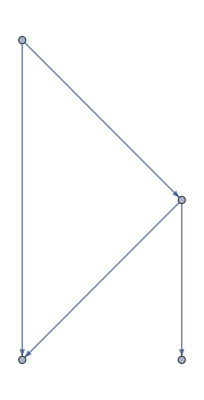

```mathematica
exercise3directed=Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"}]
```

To produce an undirected simple graph, you can set the option DirectedEdges to False.

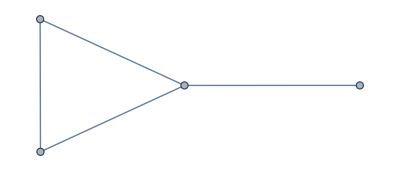

```mathematica
exercise3=Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False]
```

Note that the difference in appearance in the directed and undirected versions is a result of a preference in the Wolfram Language to draw directed graphs with arrows pointing down. In the undirected case, there is no such concern and a more compact image results.

You can also create (undirected) simple graphs using a TwoWayRule (<->, <->) or the symbol <-> in place of Rule (->, →). The undirected edge symbol is entered by typing EscueEsc.

```mathematica
Graph[{"a"<->"b","a"<->"c","b"<->"c","b"<->"d"}]
```

-Graphics-

If you prefer, you can use the symbol ->, entered as EscdeEsc in place of Rule (->) for a directed graph. In this manual, we will generally use Rule (->) to specify all edges together with the DirectedEdges option, when needed, as this frequently involves the least typing and typos do not result in mixed graphs. There are, however, some functions that apply to edges and require that you correctly distinguish between directed (using -> or EscdeEsc) and undirected edges (using <-> or EscueEsc). Pay special attention to those situations.

If you wish, you may give an explicit list of vertices as the first argument to Graph. This is only required in the situation when a graph has a vertex not adjacent to any other, as in the example below.

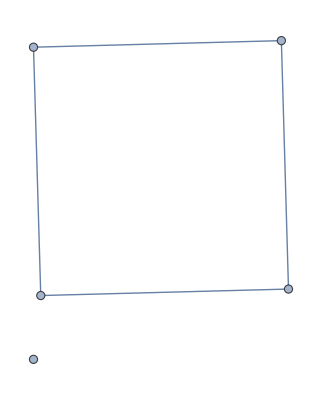

```mathematica
Graph[{1,2,3,4,5},{1->2,2->3,3->4,4->1},DirectedEdges->False]
```

The VertexList and EdgeList functions applied to a Graph object produce lists of the vertices and edges of the graph.

```mathematica
VertexList[exercise3]
```

{a,b,c,d}

```mathematica
EdgeList[exercise3]
```

{a<->b,a<->c,b<->c,b<->d}

Observe that the output of EdgeList is a list of undirected edges, using the symbol <->, despite the fact that we defined the graph using rules. This is because the effect of setting the DirectedEdges option to False is to transform the rules into undirected edges. Using FullForm, you can see that these are stored using the head UndirectedEdge.

```mathematica
EdgeList[exercise3]//FullForm
```

List[UndirectedEdge["a","b"],UndirectedEdge["a","c"],UndirectedEdge["b","c"],UndirectedEdge["b","d"]]

Note that the same is true in the directed case, with the edges represented internally as DirectedEdge.

```mathematica
EdgeList[exercise3directed]
```

{a->b,a->c,b->c,b->d}

```mathematica
EdgeList[exercise3directed]//FullForm
```

List[DirectedEdge["a","b"],DirectedEdge["a","c"],DirectedEdge["b","c"],DirectedEdge["b","d"]]

You can use DirectedEdge and UndirectedEdge yourself in creating graphs.

### Options Affecting the Visual Output of Graph

In this section, we will explain just a few of the options available for changing the visual appearance of Graph objects. Readers interested in greater control over the display of Graph objects should refer to the documentation pages.

To display the names of vertices, use the VertexLabels option. Probably the most common value for this option is "Name", including the quotation marks, which causes each vertex to be labeled with its name. As an example, we modify the definition given above of the graph from Exercise 3, with this option invoked.

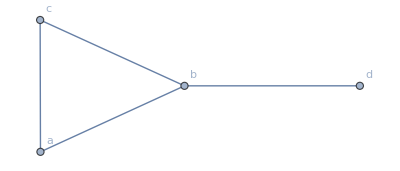

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->"Name"]
```

Another use of the VertexLabels option is to specify labels for specific vertices. You do this by identifying the option with a list consisting of rules associating the name of the vertex with the desired label. The following illustrates this by labeling two of the vertices of the graph from Exercise 3.

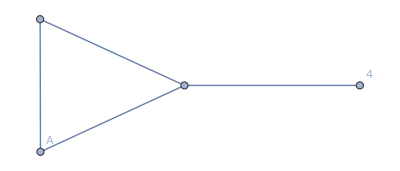

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->{"a"->"A","d"->4}]
```

The VertexLabels option can be usefully combined with the Placed symbol. The basic syntax of Placed is with a first argument being an expression to be displayed and a second argument indicating the position. Common choices for position include Above, Below, Before, After, and Center. Placed can be used with first argument “Name” in order to have all vertices labeled with their name or with a specific label for a particular vertex.

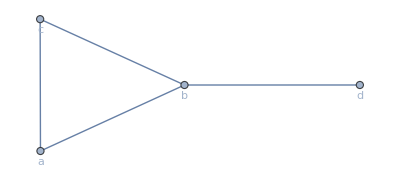

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->Placed["Name",Below]]
```

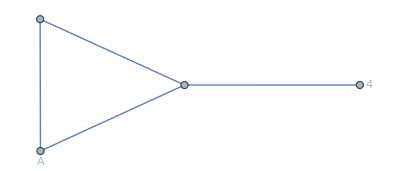

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->{"a"->Placed["A",Below],"d"->Placed[4,After]}]
```

Observe that you can combine rules specifying labels for individual vertices with a default label specification.

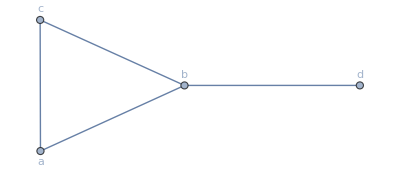

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->{"a"->Placed["Name",Below],Placed["Name",Above]}]
```

Similarly, edges in a graph can be labeled using the EdgeLabels option. Once again, the value “Name” will cause all edges to be labeled.

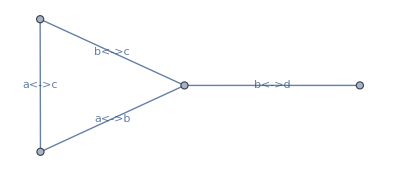

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,EdgeLabels->"Name"]
```

As with vertices, you can also choose to label specific edges with arbitrary labels by giving a list of rules as the value to EdgeLabels. When doing this, the edges should be specified using either <-> (EscueEsc) or -> (EscdeEsc); alternatively, the edge can be specified with a Rule (->) provided that the edge is surrounded by parentheses.

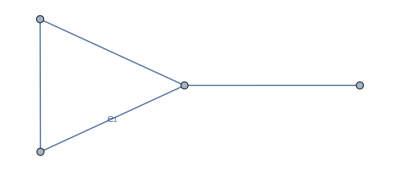

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,EdgeLabels->{"a"<->"b"->Subscript[e, 1]}]
```

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,EdgeLabels->{("a"->"b")->Subscript[e, 1]}]
```

-Graphics-

As an alternative to VertexLabels and EdgeLabels, you can use the wrapper Labeled around an edge in the list of edges or, in conjunction with the optional list of vertices, around a vertex. The first element in Labeled is the name of the vertex or the edge definition. The second element is the label to be used.

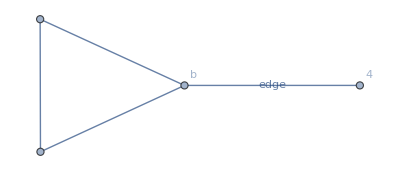

```mathematica
Graph[{"a",Labeled["b","b"],"c",Labeled["d",4]},{"a"->"b","a"->"c","b"->"c",Labeled["b"->"d","edge"]},DirectedEdges->False]
```

You can change the size of vertices with the VertexSize option. Some possible values include Tiny, Small, Medium, and Large, or a number between 0 and 1. A numerical value indicates that the size of the vertex should be that proportion of the distance between the closest two vertices. This can be used in conjunction with Placed to have vertex labels appear inside the vertex.

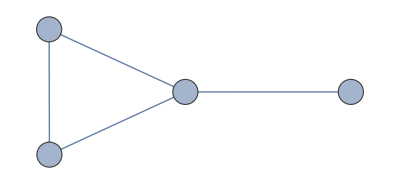

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->Placed["Name",Center],VertexSize->Medium]
```

You can further control the appearance, such as the color, of vertices and edges with the VertexStyle and EdgeStyle options. Multiple styles can be combined with the Directive wrapper. For example, the following illustrates how to create red vertices and thick green edges. Readers interested in exploring the various options available should consult the Graphics Directives guide.

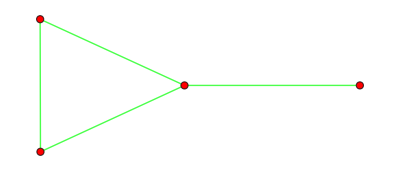

```mathematica
Graph[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexStyle->Red,EdgeStyle->Directive[Green,Thick]]
```

The VertexCoordinates option is used to specify the locations of vertices. The value for the VertexCoordinates option is a list of pairs of the form {{x_1,y_1},{x_2,y_2},...}, with the pairs specifying the coordinates of a vertex. The order of the locations must correspond to the order of the vertices in the graph. When an explicit list of vertices is given as the optional first element of Graph, that list specifies the order. Otherwise, the order is determined by when the vertex is first encountered in the list of edges, and is the same as the output of VertexList. Below, we use VertexCoordinates to redraw the graph from Exercise 3 with the vertices in the same positions as in the image in the textbook.

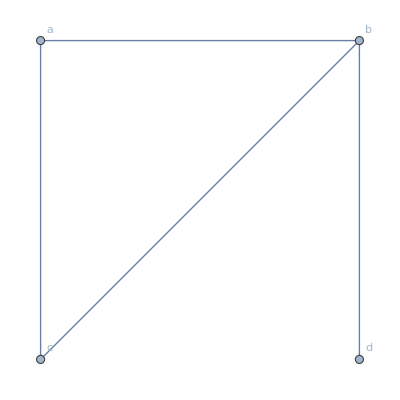

```mathematica
Graph[{"a","b","c","d"},{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->False,VertexLabels->"Name",VertexCoordinates->{{0,1},{1,1},{0,0},{1,0}}]
```

You can also exert control over the layout of the vertices of a graph, but without specifying each coordinate, by using the GraphLayout option to specify the algorithm used to choose the vertex location. Common choices include: "SpringEmbedding", which treats edges as springs and minimizes the mechanical energy of the system; "SpringElectricalEmbedding", which treats edges as springs and vertices as electrical charges and minimizes mechanical and electrical energy; "HighDimensionalEmbedding", which is like the spring-electrical method but computes in high dimensions and then projects down to two; "CircularEmbedding", which places the vertices on a circle; and "LayeredDrawing", which places vertices in layers and attempts to reduce the number of edges between non-adjacent layers.

### Modifying Graphs

Graph objects may contain loops, as illustrated below with a replica of Exercise 7 from Section 10.1. Loops are created simply by including an edge from a vertex to itself.

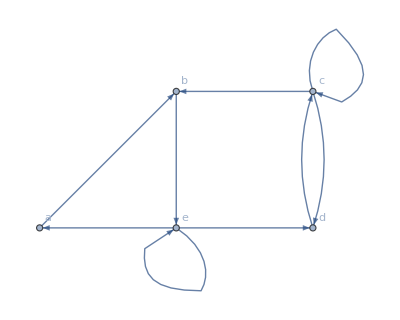

```mathematica
exercise7=Graph[{"a","b","c","d","e"},{"a"->"b","b"->"e","c"->"b","c"->"c","c"->"d","d"->"c","e"->"a","e"->"d","e"->"e"},VertexLabels->"Name",VertexCoordinates->{{1,1},{2,2},{3,2},{3,1},{2,1}}]
```

Graph objects may also include multiple edges. The following is the graph from Exercise 4 from Section 10.1.

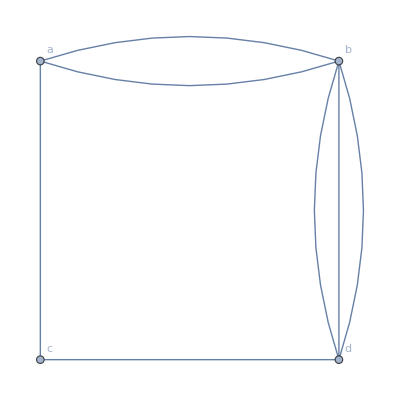

```mathematica
exercise4=Graph[{"a"->"b","a"->"b","a"->"c","b"->"d","b"->"d","b"->"d","c"->"d"},DirectedEdges->False,VertexLabels->"Name",VertexCoordinates->{{1,2},{2,2},{1,1},{2,1}}]
```

You can modify existing graphs by adding and deleting edges and vertices with the functions VertexAdd, VertexDelete, EdgeAdd, and EdgeDelete. Each of these functions requires a graph as the first argument. The second argument is usually either a vertex, an edge, or a list of vertices or edges. The deletion functions can, in place of a vertex, edge, or list, accept a pattern as the second argument in order to delete all of the vertices or edges that match the pattern.

Beginning with the graph from Exercise 4, we use VertexAdd to add two new vertices to the graph.

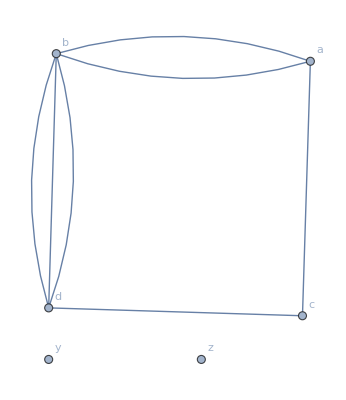

```mathematica
modifyExercise4=VertexAdd[exercise4,{"y","z"}]
```

Now, we add edges to connect the new vertices with the rest of the graph. Note that, in this example, the Wolfram Language interprets rules as undirected edges since the original graph is undirected.

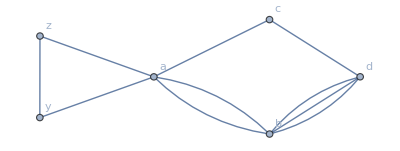

```mathematica
modifyExercise4=EdgeAdd[modifyExercise4,{"a"->"z","a"->"y","y"->"z"}]
```

Next, we delete one of the old edges. Note that to delete an edge from an undirected graph, you must use <-> (EscueEsc) or TwoWayRule (<->). Likewise, deleting an edge from a directed graph must use -> (EscdeEsc) or Rule (->).

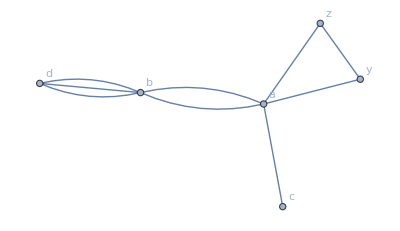

```mathematica
modifyExercise4=EdgeDelete[modifyExercise4,"d"<->"c"]
```

Note that deleting an edge between two vertices with multiple edges will delete one of the edges.

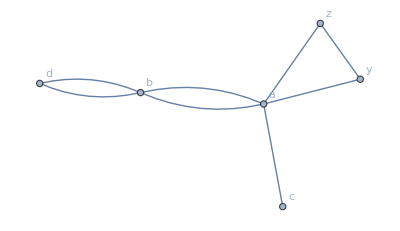

```mathematica
modifyExercise4=EdgeDelete[modifyExercise4,"d"<->"b"]
```

Finally, note that deleting a vertex also deletes all the edges incident with that vertex.

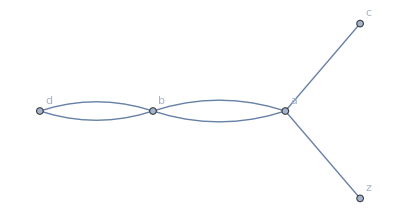

```mathematica
modifyExercise4=VertexDelete[modifyExercise4,"y"]
```

### Semantic Networks

The textbook defines semantic networks at the end of Section 10.1. Mathematica’s capabilities for working with graphs together with the extensive and growing Wolfram Knowledgebase are a powerful combination. We will create a semantic network for the word “program” using the Wolfram Knowledgebase.

The WordData function will accept a string representing a word.

```mathematica
WordData["program"]
```

{{program,Noun,Performance},{program,Noun,Idea},{program,Noun,System},{program,Noun,WrittenDocument},{program,Noun,SoftwareSystem},{program,Noun,Show},{program,Noun,Information},{program,Noun,Promulgation},{program,Verb,Schedule},{program,Verb,CreateMentally}}

The output displayed above is a list of lists, with the first member of each list being the word itself, the second being the part of speech, and the third indicating a possible “sense” of the word.

WordData accepts a second argument that allows you to get information about specific properties associated with the word. Some of the properties are “Antonyms”, “Synonyms”, “BroaderTerms”, “NarrowerTerms”, “Definitions” and “Examples”.

```mathematica
WordData["program","BroaderTerms"]
```

{{program,Noun,Performance}→{performance},{program,Noun,Idea}→{idea,thought},{program,Noun,System}→{system,system of rules},{program,Noun,WrittenDocument}→{document,papers,written document},{program,Noun,SoftwareSystem}→{computer software,package,software,software package,software program,software system},{program,Noun,Show}→{show},{program,Noun,Information}→{info,information},{program,Noun,Promulgation}→{announcement,promulgation},{program,Verb,Schedule}→{schedule},{program,Verb,CreateMentally}→{create by mental act,create mentally}}

In the graph of the semantic network for the word “program,” the terms on the right-hand side of the rules in the output above will be the neighbors of “program.” The first step is to extract all of those terms. Fortunately, WordData accepts a third argument to specify the form of the output. If we give “List” as that third argument, the output will be a list of all the terms related to “program.”

```mathematica
WordData["program","BroaderTerms","List"]
```

{announcement,computer software,create by mental act,create mentally,document,idea,info,information,package,papers,performance,promulgation,schedule,show,software,software package,software program,software system,system,system of rules,thought,written document}

We will need to create edges between “program” and each of these words, which we can do with Map.

```mathematica
Map[DirectedEdge["program",#]&,WordData["program","BroaderTerms","List"]]
```

{program->announcement,program->computer software,program->create by mental act,program->create mentally,program->document,program->idea,program->info,program->information,program->package,program->papers,program->performance,program->promulgation,program->schedule,program->show,program->software,program->software package,program->software program,program->software system,program->system,program->system of rules,program->thought,program->written document}

This is not yet a very interesting network, so we take it one step further and find the words related to those related to “program.” We use a Table to apply the technique above to all the words that appear in the list of broader terms for “program.” The result is rather long, so to save space, we limit the number of lines of output with Short.

```mathematica
Short[Table[Map[DirectedEdge[word,#]&,WordData[word,"BroaderTerms","List"]],{word,WordData["program","BroaderTerms","List"]}],10]
```

{{announcement->statement},{computer software->code,computer software->computer code},«18»,{thought->belief,thought->cognitive content,thought->content,thought->higher cognitive process,thought->mental object},{written document->piece of writing,written document->writing,written document->written material}}

Thus, the edges of the graph of this semantic network can be obtained by flattening that result and combining it with the edges incident on “program.” This graph will be too large to display the terms on the graph, so we label the vertices using Placed with second argument Tooltip, so that if you hover the mouse pointer over a vertex, it will display the term associated with the vertex.

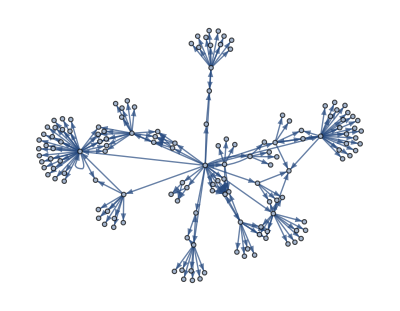

```mathematica
Graph[Join[Map[DirectedEdge["program",#]&,WordData["program","BroaderTerms","List"]],Flatten[Table[Map[DirectedEdge[word,#]&,WordData[word,"BroaderTerms","List"]],{word,WordData["program","BroaderTerms","List"]}]]],VertexLabels->Placed["Name",Tooltip]]
```

You might be surprised by the presence of a self-loop in the graph, indicating the presence of a word related to itself. Hovering the mouse over that vertex, you can see that the word in question is “show.” Applying WordData to “show” with third argument “Rules” will give detailed information, including the part of speech and sense of the word on the right-hand side of the rules. Again, this output will be long, so we use Select to find those with the word “show” on the right-hand side of the rule.

```mathematica
Select[WordData["show","BroaderTerms","Rules"],MemberQ[#[[2]],"show",2]&]
```

{{show,Verb,Register}→{{read,Verb,Indicate},{record,Verb,Indicate},{register,Verb,Indicate},{show,Verb,Read}},{show,Verb,Exhibit}→{{show,Verb,Demonstrate}}}

We see that the word “show” is related to itself in two different ways: the sense “Read” is broader than the sense “Register,” and the sense “Exhibit” is broader than the sense “Demonstrate.”

It is not always clear from the “sense” what specific definition is meant. WordData can be applied to a full word specification, that is, the list containing the word, part of speech, and sense. The second argument “Definition” or “Examples” is useful in this context.

```mathematica
WordData[{"show","Verb","Read"},"Definitions"]
```

{{show,Verb,Read}→indicate a certain reading; of gauges and instruments}

```mathematica
WordData[{"show","Verb","Register"},"Definitions"]
```

{{show,Verb,Register}→give evidence of, as of records}

```mathematica
WordData[{"show","Verb","Register"},"Examples"]
```

{{show,Verb,Register}→{The diary shows his distress that evening}}

Finally, compare the graph produced from broader terms to that consisting of synonyms. Note that, in this case, the edges are undirected, representing the symmetric nature of the synonym relation. Also note that we create the graph with SimpleGraph so as to eliminate the multiple edges.

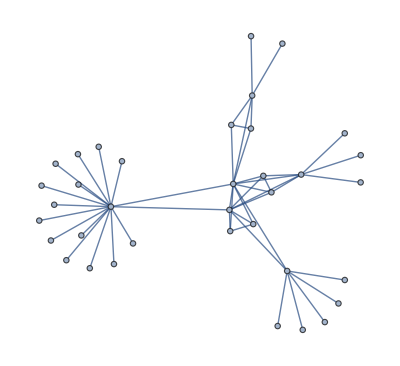

```mathematica
SimpleGraph[Join[Map[UndirectedEdge["program",#]&,WordData["program","Synonyms","List"]],Flatten[Table[Map[UndirectedEdge[word,#]&,WordData[word,"Synonyms","List"]],{word,WordData["program","Synonyms","List"]}]]],VertexLabels->Placed["Name",Tooltip]]
```

### GraphPlot

The GraphPlot function was introduced in Mathematica version 6. This function is older than and mostly superseded by the Graph object. However, GraphPlot provides some different functionality and is worth a brief discussion. Keep in mind that GraphPlot was designed specifically as a way to create images of graphs, before the Graph object was introduced, so if your focus is on creating an image of a graph and are having difficulty getting Graph to display the graph how you wish, GraphPlot is worth considering.

The most important difference between GraphPlot and Graph is the fact that Graph produces a graph object, which can be computed with and manipulated, whereas GraphPlot produces a graphics object, which is the same kind of output as Plot or Plot3D produce.

The basic input for GraphPlot is either a list of rules representing the edges of the graph or a Graph object. GraphPlot does not allow the use of the symbols <-> or ->, nor does it allow the use of TwoWayRule (<->).

We will use the graph from Exercise 3 as the example.

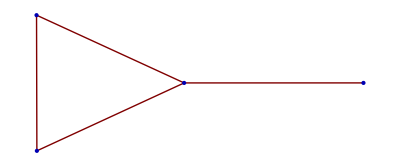

```mathematica
GraphPlot[{"a"->"b","a"->"c","b"->"c","b"->"d"}]
```

Right away, you can see an important difference between GraphPlot and Graph. Specifically, where Graph’s default behavior is to interpret rules as directed edges, GraphPlot assumes that rules are not directed. To draw a directed graph, you must use the DirectedEdges option.

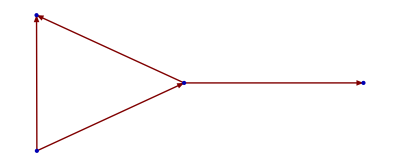

```mathematica
GraphPlot[{"a"->"b","a"->"c","b"->"c","b"->"d"},DirectedEdges->True]
```

To display the names of vertices, you use the VertexLabeling option. The default behavior, provided the number of vertices is not too large, is for the names of vertices to appear in a tooltip when you move the mouse pointer over the vertex. This option can be explicitly given with value Tooltip. By setting the VertexLabeling option to True, the names will be displayed on the graph itself.

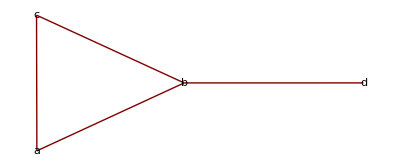

```mathematica
GraphPlot[{"a"->"b","a"->"c","b"->"c","b"->"d"},VertexLabeling->True]
```

To explicitly control the placement of vertices, you use the VertexCoordinateRules option. The value of this option is a list of rules identifying the name of a vertex with a pair representing x and y coordinates. You can use the symbol Automatic in place of the coordinate pair to indicate that Mathematica should determine the location for that vertex automatically. This is the default for vertices that are omitted from the rules. You can also use Automatic in place of either the x or y value within a pair if you wish to specify one value but leave the other to Mathematica to determine. We use VertexCoordinateRules to rearrange the vertices in the graph from Exercise 3 to match the locations in the textbook.

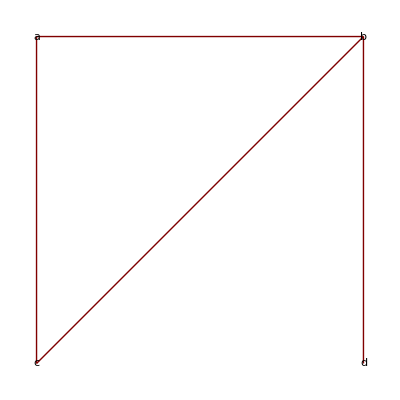

```mathematica
GraphPlot[{"a"->"b","a"->"c","b"->"c","b"->"d"},VertexLabeling->True,VertexCoordinateRules->{"a"->{0,1},"b"->{1,1},"c"->{0,0},"d"->{1,0}}]
```

One of the benefits of GraphPlot is that the displayed graphic can be dynamically manipulated. The code below produces default display of the graph from Exercise 3. If you double-click on the image and then double-click on a vertex (so that the vertex is highlighted), you can adjust the position of the vertex by dragging it. Below, we have moved vertex “d” into the center of the graph. Observe that the edge automatically adjusts.

```mathematica
GraphPlot[{"a"->"b","a"->"c","b"->"c","b"->"d"},VertexLabeling->True]
```

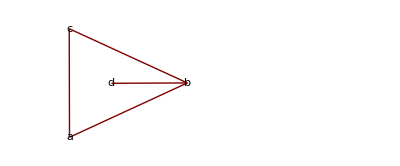

## 10.2 Graph Terminology and Special Types of Graphs

In this section, we will see how to use Mathematica to perform computations related to some of the basic terminology of graphs, such as calculating degree. We will also look at some of the special families of graphs included in the Wolfram Language. Finally, we will discuss subgraphs and unions of graphs.

### Degree

For a Graph object, the Wolfram Language includes the function VertexDegree for determining the degree of a vertex. Given a Graph object and one of the graph’s vertices, the function returns the number of edges incident to that vertex. For example, we can check the degrees of vertices a and e of exercise7 from the previous section.

```mathematica
exercise7
```

-Graphics-

```mathematica
VertexDegree[exercise7,"a"]
```

2

```mathematica
VertexDegree[exercise7,"e"]
```

5

Observe that the loop at the vertex e counts as 2 towards the degree of that vertex. Moreover, note that with this directed graph, VertexDegree calculates the number of edges incident to the given vertex without regard for their direction. The Wolfram Language includes VertexInDegree and VertexOutDegree for calculating the directed values. As an example, consider vertex d from above.

```mathematica
VertexInDegree[exercise7,"d"]
```

2

```mathematica
VertexOutDegree[exercise7,"d"]
```

1

All three of these functions can be used without a second argument. If they are passed only the graph as the sole argument, they will return a list of the degrees of the vertices. Note that the output is in the same order as the output from VertexList.

```mathematica
VertexList[exercise7]
```

{a,b,c,d,e}

```mathematica
VertexDegree[exercise7]
```

{2,3,5,3,5}

```mathematica
VertexInDegree[exercise7]
```

{1,2,2,2,2}

```mathematica
VertexOutDegree[exercise7]
```

{1,1,3,1,3}

### Some Special Simple Graphs

The textbook discusses several families of graphs, including complete graphs, cycles, and wheels. The Wolfram Language provides functions for easily creating these and other special graphs.

We begin with complete graphs. Recall that a complete graph is a simple, undirected graph on a given number of vertices that has all possible edges between those vertices. The complete graph on n vertices is denoted K_n. The complete graph on n vertices can be obtained with the function CompleteGraph applied to n. For example, we can generate and display K_5, the complete graph on 5 vertices.



```mathematica
CompleteGraph[5]
```

Similarly, the cycle C_n is obtained with the function CycleGraph.

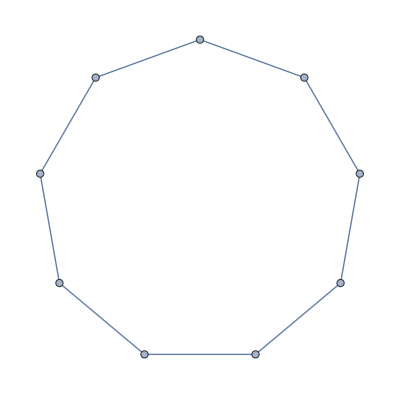

```mathematica
CycleGraph[9]
```

A wheel W_n is obtained from the cycle graph C_n by adding one additional vertex adjacent to all n of the original vertices. In the Wolfram Language, wheel graphs are obtained by WheelGraph applied to the value n+1, the total number of vertices in the wheel, not just the outside ring.

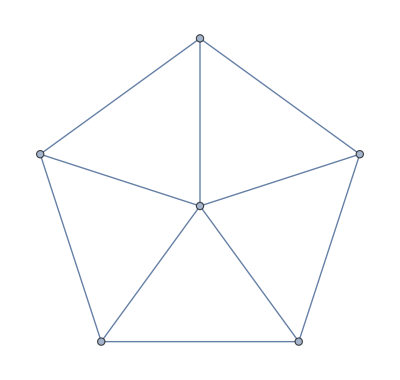

```mathematica
WheelGraph[6]
```

### Hypercubes

To construct the n-cube Q_n, we use the HypercubeGraph function applied to the dimension n. Recall the definition of the hypercube graph given in Example 8 of Section 10.2. There are 2^n vertices labeled with the binary representations of the numbers 0 through 2^n-1. Two vertices are adjacent if their binary representations differ in only one digit. Here is the presentation of the three-dimensional cube.

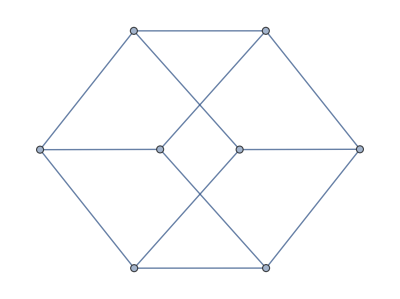

```mathematica
HypercubeGraph[3]
```

By default, the vertices are not labeled. To have label the vertices, we can use the VertexLabels option. While the named parametric graphs generally accept all the same options that Graph does, HypercubeGraph in particular is more robust passed to Graph.

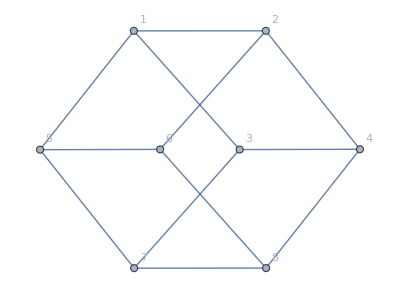

```mathematica
Graph[HypercubeGraph[3],VertexLabels->"Name"]
```

One more modification will allow us to see the connection between this image and the definition. Instead of using “Name” as the argument to VertexLabels, we can specify the labels explicitly by setting the option to a list of rules identifying the integers with the binary expression.

The definition of Q_n tells us that the vertices should be considered to be the binary representations of the integers from 0 to 7. To display this, we will apply labels by subtracting 1 from the integer vertex names and using the IntegerString function to obtain the binary representation. The IntegerString function requires two arguments, an integer and a base, and produces a string representing the integer in that base. A third optional argument allows you to specify a minimal length for the string.

The following Table produces a list of rules identifying the vertex names with the appropriate label.

```mathematica
Table[v->IntegerString[v-1,2,3],{v,8}]
```

{1→000,2→001,3→010,4→011,5→100,6→101,7→110,8→111}

We can combined this with the Placed symbol to move the labels inside the vertices. Be warned that, while this is an effective method in general, it can cause the kernel to crash when passed as an option directly to HypercubeGraph. If this happens, passing the HypercubeGraph as an option to the more general Graph can fix the problem.

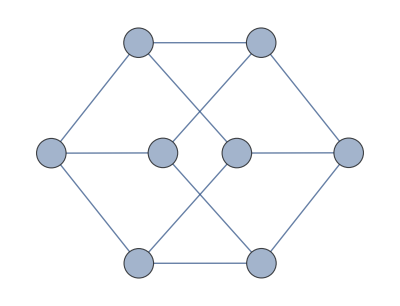

```mathematica
Graph[HypercubeGraph[3],VertexLabels->Table[v->Placed[IntegerString[v-1,2,3],Center],{v,8}],VertexSize->Large]
```

### Bipartite Graphs

Another important class of graphs is the bipartite graphs. A bipartite graph is one whose vertex set can be partitioned into two disjoint sets such that every edge has one vertex in each of the partitioning sets. In other words, no two vertices in the same partitioning set are adjacent. We write V=(A,B) to indicate that the vertex set V is partitioned into the sets A and B.

The complete bipartite graph K_(m,n) is a bipartite graph with bipartition V=(A,B) such that there are m vertices in A and n in B and such that there is an edge for every pair of vertices a∈A and b∈B. The CompleteGraph function can be used to create complete bipartite graphs. The argument is the list consisting of the pair of m and n.

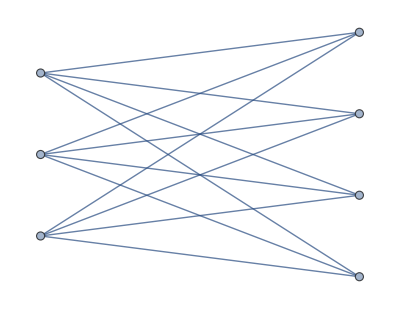

```mathematica
CompleteGraph[{3,4}]
```

Notice that Mathematica draws the complete bipartite graph with the two partitioning sets along the left and right to make the partition visually clear. As with the other functions in this section, the usual options for Graph apply. We illustrate how to label the vertices in a meaningful way. To enter a subscript in Mathematica, press Ctrl and -.

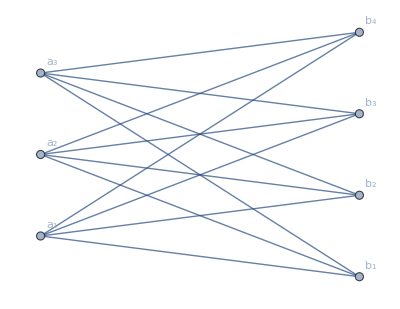

```mathematica
CompleteGraph[{3,4},VertexLabels->Union[Table[i->Subscript[a, i],{i,3}],Table[i->Subscript[b, i-3],{i,4,7}]]]
```

The Wolfram Language also supports complete multipartite graphs. A k-partite graph is a graph in which the vertices can be partitioned into k disjoint sets so that no two vertices in any one of the partitioning sets are adjacent.

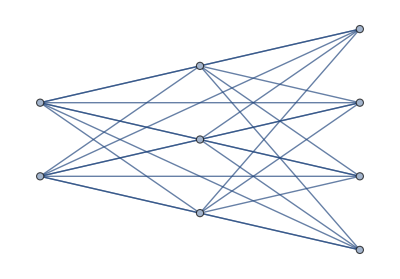

```mathematica
CompleteGraph[{2,3,4}]
```

The function BipartiteGraphQ determines whether a given graph is bipartite. This function accepts a graph as its sole argument and returns True if the graph is bipartite.

```mathematica
BipartiteGraphQ[HypercubeGraph[3]]
```

True

#### Bipartition

It is worthwhile, however, to create a version of BipartiteGraphQ from scratch in order to better understand both the representation of graphs in the Wolfram Language and an algorithm that determines whether the graph is bipartite and finds a bipartition. Our function will apply to a Graph object. Moreover, instead of just returning true, our function will, if the graph is bipartite, display the graph with the vertices colored red and green to represent the partitioning. Of course, if the graph is not bipartite, the function will return false.

For Graph objects, the colors of vertices can be changed by setting the VertexStyle option to a single style for global changes or to a list of rules to set options for individual vertices as is shown below.

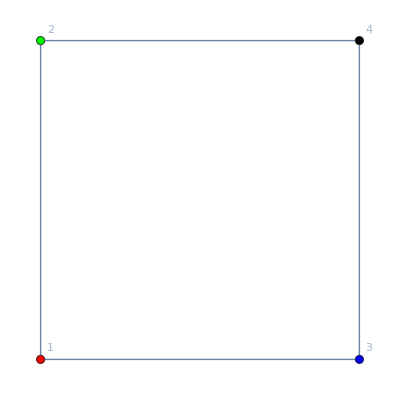

```mathematica
Graph[HypercubeGraph[2],VertexLabels->"Name",VertexStyle->{1->Red,2->Green,3->Blue,4->Black}]
```

In addition to the color, the shape of the vertices can be changed using the VertexShapeFunction option. This option can be used to take full control over the drawing of vertices by defining a function that builds the vertex out of graphics primitives. Fortunately, there are also a variety of predefined shape functions, as illustrated below.

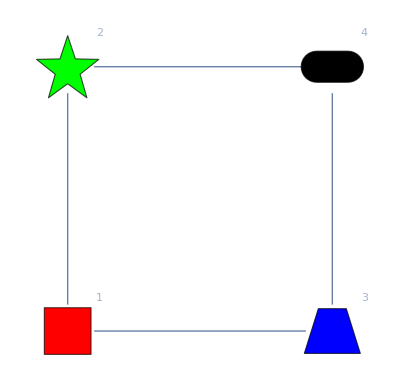

```mathematica
Graph[HypercubeGraph[2],VertexLabels->"Name",VertexStyle->{1->Red,2->Green,3->Blue,4->Black},
VertexShapeFunction->{1->"Square",2->"Star",3->"UpTrapezoid",4->"Capsule"},VertexSize->Medium]
```

Our version of BipartiteGraphQ will need to determine the list of neighbors of a given vertex. For a Graph object, the built-in function AdjacencyList applied to a graph and a vertex will return the list of vertices adjacent to it. However, we will create our own version of this to better illustrate how to manipulate graphs on a basic level.

To find the neighbors of a vertex in a Graph object, we need to find all of the edges containing the given vertex and output the other vertex in the edge. The Cases function can be used for this. The first argument to Cases is a list of expressions. The second argument is a pattern expressing which elements of the first argument should be output. In our case, we want to pick out those edges, one of whose elements is the desired vertex.

Before applying Cases we need to extract the edges from the Graph and determine what patterns to look for. The EdgeList function returns a list of the edges of a graph. If we apply FullForm as well, we can see the internal structure. We use the graph from Exercise 3 in Section 10.1, which we defined above, as an example.

```mathematica
exercise3
```

-Graphics-

```mathematica
EdgeList[exercise3]//FullForm
```

List[UndirectedEdge["a","b"],UndirectedEdge["a","c"],UndirectedEdge["b","c"],UndirectedEdge["b","d"]]

Observe that this is a list of pairs of vertices with the head UndirectedEdge. If the edges were directed, the head would be DirectedEdge.

Consider the following graph, with both directed and undirected edges.

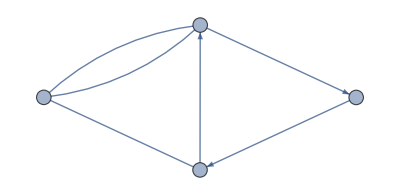

```mathematica
partitionExample=Graph[{1->2,2->3,3->1,3<->4,1<->4,1<->4},VertexLabels->Placed["Name",Center],VertexSize->Small]
```

Suppose we are looking for edges involving the vertex 3. Those edges will either be of the form Head[3,_] or Head[_,3], where Head is either DirectedEdge or UndirectedEdge. In a pattern, we use the Alternatives (|) operator to combined two or more possibilities in a single pattern. The following picks out all of the edges incident to vertex 3 in partitionExample.

```mathematica
EdgeList[partitionExample]
```

{1->2,2->3,3->1,3<->4,1<->4,1<->4}

```mathematica
Cases[EdgeList[partitionExample],DirectedEdge[3,_]|DirectedEdge[_,3]|UndirectedEdge[3,_]|UndirectedEdge[_,3]]
```

{2->3,3->1,3<->4}

Note that these edges form the neighborhood graph of vertex 3, that is, the subgraph consisting of vertex 3 and all of its neighbors. However, our interest is the vertices, not the edges. To obtain the vertices, we will take advantage of another feature of the Cases function: the second argument can be given as a rule. The left-hand side of the rule is the pattern expressing which elements of the original list should match and the right-hand side describes what to include in the output for that matching element. Since we want the other vertex in the output, not the entire rule, we will name the blanks in the rule and output the vertex.

```mathematica
Cases[EdgeList[partitionExample],DirectedEdge[3,x_]|DirectedEdge[x_,3]|UndirectedEdge[3,x_]|UndirectedEdge[x_,3]:>x]
```

{2,1,4}

Note that we use RuleDelayed (:>, :>) to protect against the symbol x having been assigned a value elsewhere. It is a good idea to use SetDelayed (:=) and RuleDelayed (:>, :>) when named blanks are involved.

Applying Union will remove duplicates and sort the results. Replacing the example data with arguments allows us to create a function.

```mathematica
neighbors[g_Graph,v_]:=Union[Cases[EdgeList[g],DirectedEdge[v,x_]|DirectedEdge[x_,v]|UndirectedEdge[v,x_]|UndirectedEdge[x_,v]:>x]]
```

We now turn to our version of BipartiteGraphQ. The idea of the function is as follows. (Note that this method is based on forming a spanning tree of the graph, a concept discussed in Section 11.4 of the textbook).

Pick a vertex v from the vertex set and place it in the set A.

Place all of v’s neighbors in set B.

For each vertex w in the set B that has not already been processed, place all of w’s neighbors that are not already in either set into the set A.

Repeat step 3, reversing A and B until no more vertices remain to be processed.

Once step 4 is complete, we have formed a disjoint partition of the vertices. We then examine each edge of the graph and ensure that no edge has both ends in A or both ends in B. If some edge fails that test, then the graph is not bipartite. If all of the edges do pass the test, then the graph is bipartite and (A,B) is a bipartition.

In the implementation, rather than using two sets A and B, we use the symbol AB as an indexed variable, with AB[0] representing one set and AB[1] the other. This allows us to refer to them both as AB[i] and vary i.

```mathematica
drawBipartite[g_Graph]:=Module[{V,AB,i,T,w,e},
V=VertexList[g];
w=V[[1]];
AB[0]={w};
AB[1]={};
i=0;
While[V≠{},
T=Intersection[V,AB[i]];
i=Mod[i+1,2];
Do[AB[i]=Union[AB[i],Complement[neighbors[g,w],Union[AB[0],AB[1]]]]
,{w,T}];
V=Complement[V,T]
];
Catch[
Do[If[(MemberQ[AB[0],e[[1]]]&&MemberQ[AB[0],e[[2]]])||(MemberQ[AB[1],e[[1]]]&&MemberQ[AB[1],e[[2]]]),Throw[False]]
,{e,EdgeList[g]}];
Graph[g,VertexStyle->Union[Table[i->Green,{i,AB[0]}],Table[i->Yellow,{i,AB[1]}]],VertexShapeFunction->Table[i->"Square",{i,AB[0]}]]
]
]
```

Note that if the graph is not bipartite, such as the graph H from Figure 8 in Section 10.3 of the textbook, the function will output false.

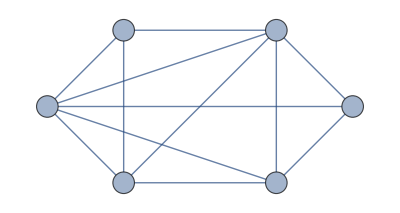

```mathematica
figure8H=Graph[{"a","b","c","d","e","f"},{"a"->"b","a"->"e","a"->"f","b"->"c","b"->"d","b"->"e","b"->"f","c"->"d","c"->"f","d"->"e","d"->"f","e"->"f"},DirectedEdges->False,VertexCoordinates->{{1,2},{3,2},{4,1},{3,0},{1,0},{0,1}},VertexLabels->Placed["Name",Center],VertexSize->Medium]
```

```mathematica
drawBipartite[figure8H]
```

False

On the other hand, if the graph is bipartite, such as the graph G shown in Figure 8 from Section 10.3, the function will draw the graph with the vertices colored to illustrate the bipartition. Note the use of GraphLayout in the initial creation of graph G below. The help page lists possible layout options. Of course, you can always specify vertex locations manually with VertexCoordinates, as above, or omit both options and Mathematica will choose a placement for you.

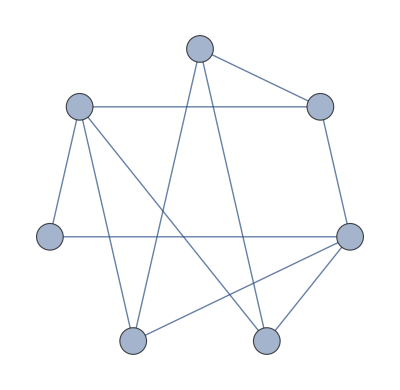

```mathematica
figure8G=Graph[{"a","g","f","e","d","c","b"},{"a"->"c","a"->"e","a"->"f","a"->"g","b"->"c","b"->"e","b"->"f","c"->"d","d"->"e","d"->"f","d"->"g"},DirectedEdges->False,GraphLayout->"CircularEmbedding",VertexLabels->Placed["Name",Center],VertexSize->Medium]
```

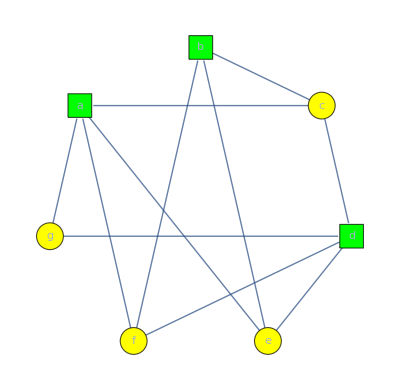

```mathematica
drawBipartite[figure8G]
```

Observe that applying our function has preserved the layout of the original. This is typical for Wolfram Language functions that apply to Graph objects. Because the options are part of the data that make up the Graph, the options are passed along to any functions that act on the Graph.

For convenience, we define a version of drawBipartite that can accept additional Graph options and pass them through our function to where we create the new Graph. The easiest way to do this is to add a BlankNullSequence (___) to the arguments of our function. The result is that the function requires a Graph as the first argument, but can accept any number of additional arguments or no additional arguments. We then just pass these to Graph.

```mathematica
drawBipartite[g_Graph,opts___]:=Module[{V,AB,i,T,w,e},
V=VertexList[g];
w=V[[1]];
AB[0]={w};
AB[1]={};
i=0;
While[V≠{},
T=Intersection[V,AB[i]];
i=Mod[i+1,2];
Do[AB[i]=Union[AB[i],Complement[neighbors[g,w],Union[AB[0],AB[1]]]]
,{w,T}];
V=Complement[V,T]
];
Catch[
Do[If[(MemberQ[AB[0],e[[1]]]&&MemberQ[AB[0],e[[2]]])||(MemberQ[AB[1],e[[1]]]&&MemberQ[AB[1],e[[2]]]),Throw[False]]
,{e,EdgeList[g]}];
Graph[g,VertexStyle->Union[Table[i->Green,{i,AB[0]}],Table[i->Yellow,{i,AB[1]}]],VertexShapeFunction->Table[i->"Square",{i,AB[0]}],opts]
]
]
```

For example, we might want to draw the edges dashed.

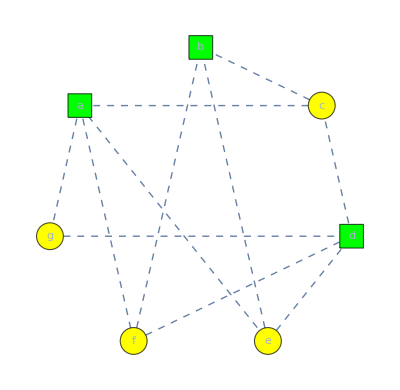

```mathematica
drawBipartite[figure8G,EdgeStyle->Dashed]
```

### Bipartite Graphs and Matchings

Mathematica can help us find maximal matchings in a bipartite graph. We will use Figure 10a from Section 10.2 of the text as an example. To improve readability, we have abbreviated the names to their first letter and shortened the descriptions of the jobs.

```mathematica
figure10aEdges={"A"->"req","A"->"test","B"->"arch","B"->"imp","B"->"test","C"->"req","C"->"arch","C"->"imp","D"->"req"}
```

{A→req,A→test,B→arch,B→imp,B→test,C→req,C→arch,C→imp,D→req}

In order to draw the graph meaningfully, in the same fashion as in the text, we will specify the coordinates of each vertex. This is done by setting the VertexCoordinates option to a list of coordinates, with the order of the list matching the order of the vertices. To ensure that our order is correct, we will specify a vertex list when we create the Graph.

```mathematica
figure10aVertices={"A","B","C","D","req","test","arch","imp"}
```

{A,B,C,D,req,test,arch,imp}

To create the list of coordinates, we use Table twice and specify that the names should have y-coordinate 1 and the jobs should have y-coordinate 0. Join is used to combine the two lists.

```mathematica
figure10aCoordinates=Join[Table[{i,1},{i,4}],Table[{i,0},{i,4}]]
```

{{1,1},{2,1},{3,1},{4,1},{1,0},{2,0},{3,0},{4,0}}

We now create the graph.

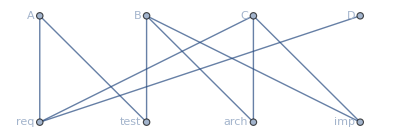

```mathematica
figure10a=Graph[figure10aVertices,figure10aEdges,DirectedEdges->False,VertexLabels->Placed["Name",Before],VertexCoordinates->figure10aCoordinates]
```

To find a maximal matching, we use the function FindIndependentEdgeSet. The term independent edge set is synonymous with matching. The only allowed argument to this function is the graph. It returns a list of edges in a matching.

```mathematica
figure10aMatching=FindIndependentEdgeSet[figure10a]
```

{A<->test,B<->imp,C<->arch,D<->req}

The output indicates that one maximal matching has Alvarez assigned to testing, Berkowitz to implementation, Chen to architecture, and Davis to requirements.

We can visualize this matching by highlighting the edges that form the matching using the function HighlightGraph. This function requires two arguments. The first is a graph. The second is a list of the elements to highlight. In this case, the second argument will be the output from FindIndependentEdgeSet.

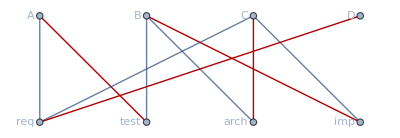

```mathematica
HighlightGraph[figure10a,figure10aMatching]
```

### Subgraphs and Induced Subgraphs

The Wolfram Language provides the Subgraph function for producing a subgraph from an existing graph. Given a graph and a list of edges, Subgraph produces the Graph consisting of the edges and all the vertices that are an endpoint of one of the given edges.

For example, we create the circulant graph with 6 vertices and jump 2, and then create the subgraph consisting of one of triangles. A circulant graph on n vertices with jump j is a graph with vertices {1,2,…,n}, typically arranged in a circle, and such that vertex u is connected to vertex v whenever u≠v and u≡v (mod j). Visually, each vertex is connected to the vertex j further around the circle.

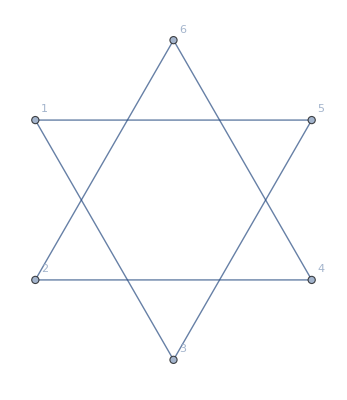

```mathematica
star=CirculantGraph[6,2,VertexLabels->"Name"]
```

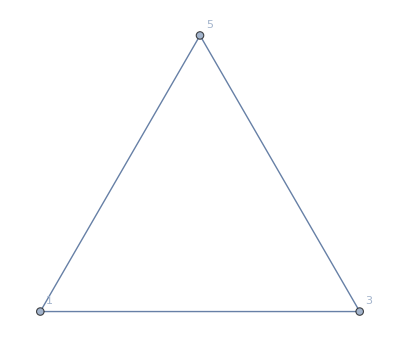

```mathematica
substar=Subgraph[star,{1->3,3->5,5->1},VertexLabels->"Name"]
```

Alternatively, you can give a list of vertices as the second argument to Subgraph. The result is the graph induced by the given vertices, that is, the graph consisting of the vertices and all the edges from the original graph with both endpoints in the set of vertices. Below we consider a prism graph and one of its layers.

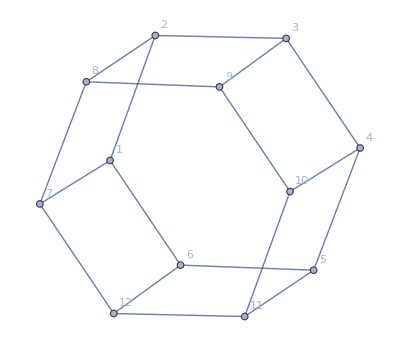

```mathematica
prism=Graph[{1->2,2->3,3->4,4->5,5->6,6->1,7->8,8->9,9->10,10->11,11->12,12->7,1->7,2->8,3->9,4->10,5->11,6->12},DirectedEdges->False,VertexLabels->"Name"]
```

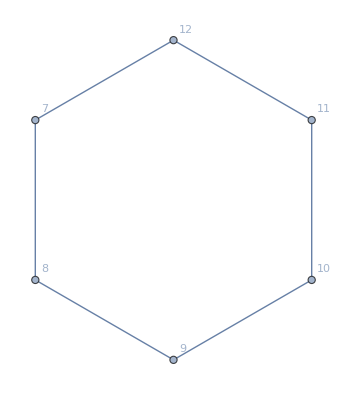

```mathematica
subprism=Subgraph[prism,{7,8,9,10,11,12},VertexLabels->"Name"]
```

The HighlightGraph function can be used to display a subgraph relative to the original by passing the original graph as the first argument and the subgraph as the second.

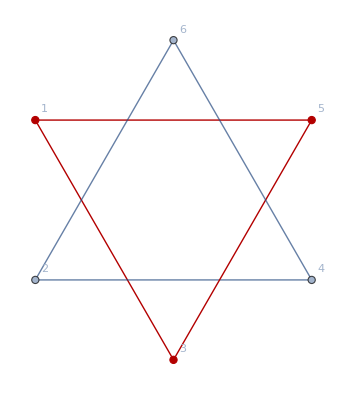

```mathematica
HighlightGraph[star,substar]
```

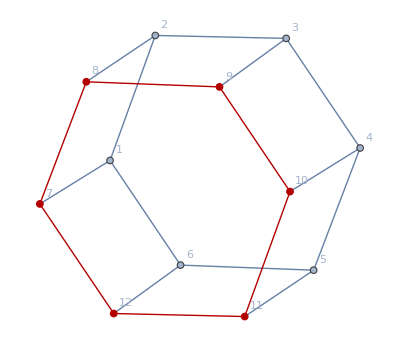

```mathematica
HighlightGraph[prism,subprism]
```

Note that the second argument of HighlightGraph can be a list of subgraphs. Below, we highlight the three triangles in the circulant graph on 9 vertices with jump 3.

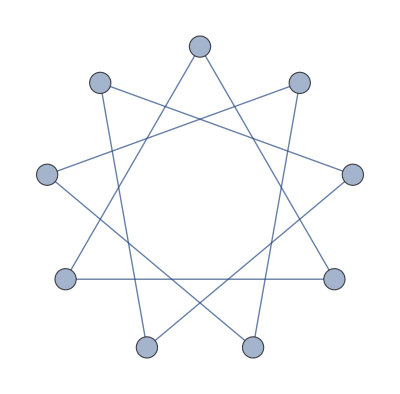

```mathematica
circulant9=CirculantGraph[9,3,VertexLabels->Placed["Name",Center],VertexSize->Medium]
```

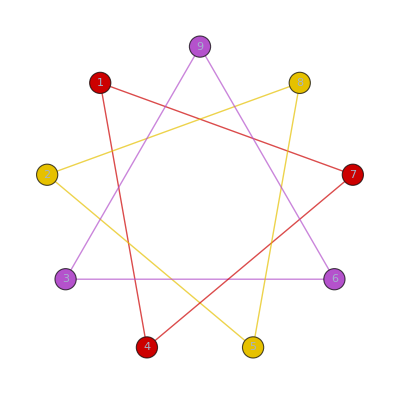

```mathematica
HighlightGraph[circulant9,Table[Subgraph[circulant9,{i,i+3,i+6}],{i,3}]]
```

### Deleting Vertices and Edges

Subgraphs can also be produced by deleting vertices or edges. The VertexDelete and EdgeDelete functions were described in Section 10.1 of this manual, but are worth revisiting. VertexDelete takes two arguments: a graph and a vertex or list of vertices. The function returns a new graph with the vertex or vertices and all incident edges removed. Here we highlight the subgraph of the complete graph K_4 that is obtained by deleting a vertex.

```mathematica
deleteVExStart=CompleteGraph[5];
```

```mathematica
deleteVExEnd=VertexDelete[deleteVExStart,1];
```

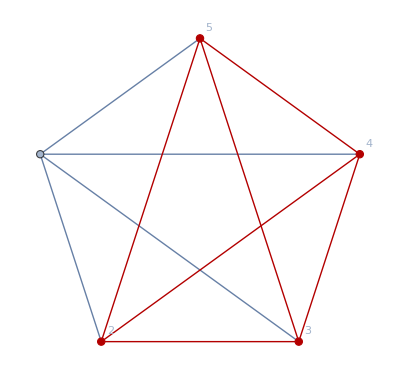

```mathematica
HighlightGraph[deleteVExStart,deleteVExEnd,VertexLabels->"Name"]
```

EdgeDelete also takes two arguments, a graph and an edge or a list of edges. For example, we can remove the outer ring of K_5 as follows:

```mathematica
deleteEexStart=CompleteGraph[5];
```

```mathematica
deleteEexEdges=Join[Table[i->i+1,{i,1,4}],{1->5}];
```

```mathematica
deleteEexEnd=EdgeDelete[deleteEexStart,deleteEexEdges];
```

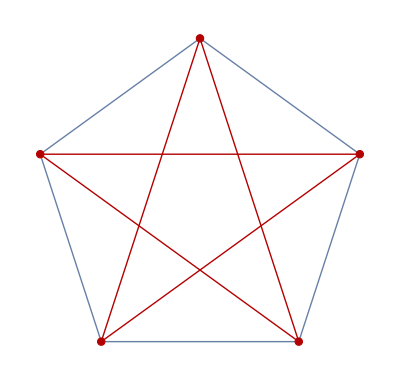

```mathematica
HighlightGraph[deleteEexStart,deleteEexEnd]
```

### Adding Vertices and Edges

The functions for adding vertices and edges are very similar. VertexAdd accepts a graph and either a vertex or list of vertices to add to the graph.

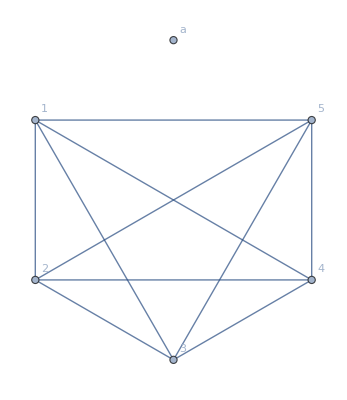

```mathematica
VertexAdd[CompleteGraph[5,VertexLabels->"Name"],"a"]
```

EdgeAdd acts on a graph and adds an edge or a list of edges. Note that you can use rules to describe the edges and Mathematica will interpret them as directed or not depending on whether the original graph is directed.

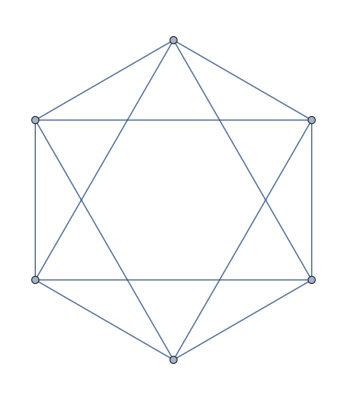

```mathematica
EdgeAdd[CycleGraph[6],{1->3,2->4,3->5,4->6,5->1,6->2}]
```

You can specify directed edges using DirectedEdge or <-> (EscueEsc); you can specify undirected edges by UndirectedEdge, -> (EscdeEsc), or TwoWayRule (<->). When a graph includes any directed edges, Rule (->) will be interpreted as a directed edge.

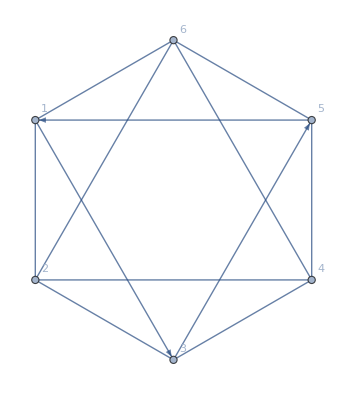

```mathematica
EdgeAdd[CycleGraph[6,VertexLabels->"Name"],{DirectedEdge[1,3],3->5,5->1,UndirectedEdge[4,6],2<->4,6<->2}]
```

### Edge Contraction

Recall that an edge contraction for an edge e with endpoints u and v consists of deleting the edge, merging u and v into a new vertex w, and preserving all edges (other than e) which had u or v as an endpoint by setting w as the new endpoint. As an illustration, consider the graph shown below.

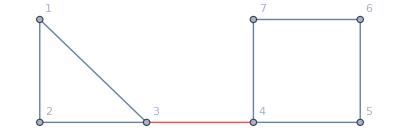

```mathematica
exampleContraction=Graph[{1,2,3,4,5,6,7},{1->2,1->3,2->3,Style[3->4,{Thick,Red}],4->5,4->7,5->6,6->7},DirectedEdges->False,VertexLabels->"Name",VertexCoordinates->{{0,1},{0,0},{1,0},{2,0},{3,0},{3,1},{2,1}}]
```

Observe the use of the Style wrapper on the edge between vertices 3 and 4 to highlight that edge.

The function EdgeContract can be used to contract an edge. It takes two arguments: a graph and an edge or list of edges.

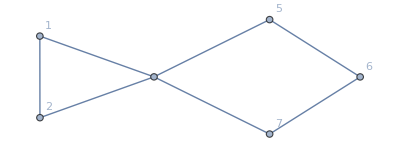

```mathematica
EdgeContract[exampleContraction,3->4]
```

The Wolfram Language also includes a similar function, VertexContract. The second argument of VertexContract is a list of vertices, and the result is the graph obtained by combining all the vertices in the list into a single vertex and removing all edges between the merged vertices. When the vertices are the endpoints of an edge, the effect is the same as EdgeContract.

```mathematica
VertexContract[exampleContraction,{3,4}]
```

-Graphics-

The second argument, however, is not limited to two vertices, nor do they need to be adjacent, as the example below illustrates.

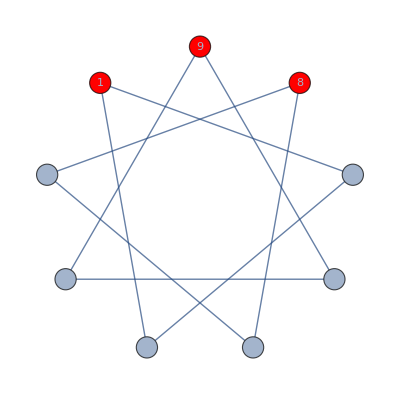

```mathematica
exampleContraction2=CirculantGraph[9,3,VertexLabels->Placed["Name",Center],VertexSize->Medium,VertexStyle->Table[i->Red,{i,{1,9,8}}]]
```

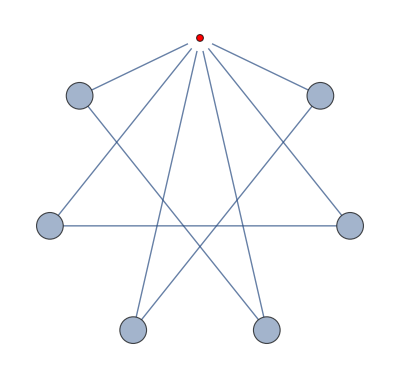

```mathematica
Graph[VertexContract[exampleContraction2,{9,1,8}],VertexStyle->{9->Red}]
```

Note that when the vertices are merged, the new vertex is given the name of the vertex that appears first in the list. Observe above that we listed 9 first in the set of vertices, and so it is 9 that we style as red. That the new vertex is unnumbered and smaller than before illustrates that the result of the contraction function is to delete all the original vertices, along with all options attached to them. Also observe that the contraction functions do not accept the options available to Graph, so we had to apply Graph to the result of the contraction.

### Unions and Complements of Graphs

Recall that the union of two graphs is the graph obtained by taking the union of the sets of vertices and the sets of edges from the two graphs.

As an example, we will “fill in” a prism graph by computing the union of the prism with the complete graph on the vertices in one ring. We begin with a version of the prism we created above.

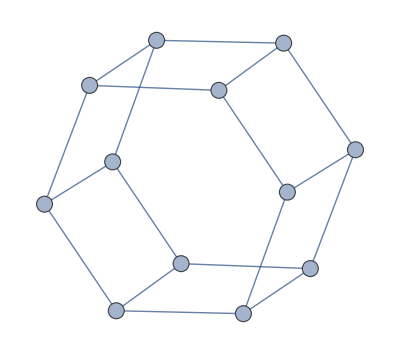

```mathematica
unionExampleA=Graph[{1->2,2->3,3->4,4->5,5->6,6->1,7->8,8->9,9->10,10->11,11->12,12->7,1->7,2->8,3->9,4->10,5->11,6->12},DirectedEdges->False,VertexLabels->Placed["Name",Center],VertexSize->Medium]
```

We use the complete graph on 6 vertices as the second graph that will form part of the union. By default, CompleteGraph with argument 6 will form the complete graph on the vertices from 1 through 6. Suppose instead that we want the complete graph on the vertices from 7 through 12. To do this, apply the VertexReplace function. This function accepts two arguments: a graph and a list of rules specifying how to modify the names of the vertices. In this instance, we will replace vertex 1 with 7, 2 with 8, and so on, so we need to use the list of rules {1→7,2→6,…,6→12}, which we will create with a Table.

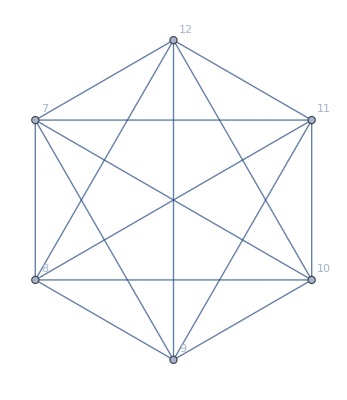

```mathematica
unionExampleB=VertexReplace[CompleteGraph[6,VertexLabels->"Name"],Table[i->i+6,{i,6}]]
```

Note that the same effect can be obtained with the function IndexGraph, with first argument a graph and second argument the smallest integer to be used (defaulting to 1 if the second argument is omitted). VertexReplace is the more general function.

Also note that this is not the same as setting different labels for the vertices. The result of VertexReplace is a graph with the internal names of the vertices changed.

```mathematica
VertexList[unionExampleB]
```

{7,8,9,10,11,12}

To obtain the union of the graphs, we apply the GraphUnion function, which simply takes the two (or more) graphs as arguments, along with the usual options.

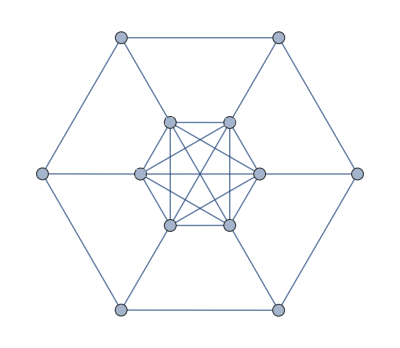

```mathematica
unionExample=GraphUnion[unionExampleA,unionExampleB,VertexLabels->Placed["Name",Center],VertexSize->Medium]
```

Note that Mathematica has rearranged the locations of the vertices. If you prefer the three-dimensional appearance of the prism, you can impose those locations by setting the VertexCoordinates property when performing the union. The GraphEmbedding function applied to a graph returns a list of all the coordinates of the vertices. Since we did not add any new vertices here, we can simply apply GraphEmbedding to the original graph.

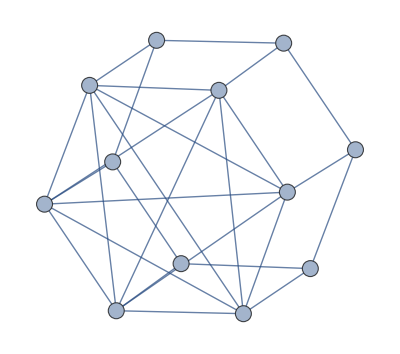

```mathematica
unionExample=GraphUnion[unionExampleA,unionExampleB,VertexLabels->Placed["Name",Center],VertexSize->Medium,VertexCoordinates->GraphEmbedding[unionExampleA]]
```

Finally, we consider graph complements, described in Exercise 61 of Section 10.2. The complement, Ḡ, of a graph G is the graph whose vertex set is the same as that of G, but whose edge set is the set of all pairs of G that have no edge between them. In other words, if G has n vertices, then the edge set of G is the complement of the edge set of G relative to K_n, the complete graph on n vertices. The Wolfram Language has a function to compute the complement of a graph: GraphComplement.

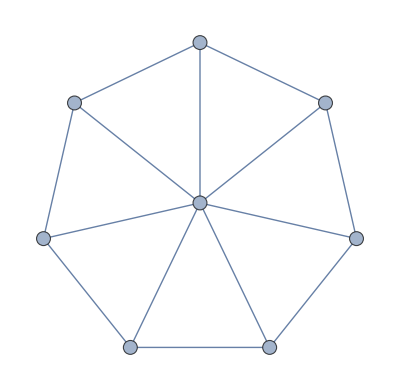

```mathematica
WheelGraph[8,VertexLabels->Placed["Name",Center],VertexSize->Small]
```

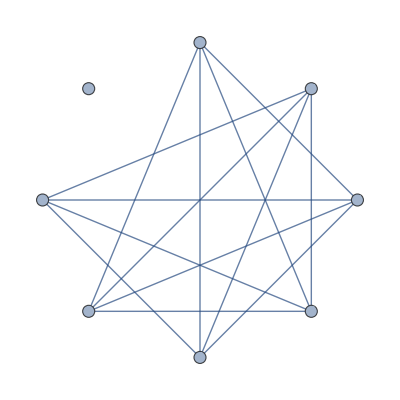

```mathematica
GraphComplement[WheelGraph[8],VertexLabels->Placed["Name",Center],VertexSize->Small]
```

Again, Mathematica has rearranged the vertices. We can impose the original locations as follows.

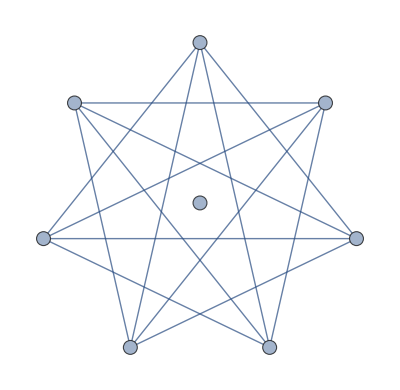

```mathematica
complementExample=GraphComplement[WheelGraph[8],VertexLabels->Placed["Name",Center],VertexSize->Small,VertexCoordinates->GraphEmbedding[WheelGraph[8]]]
```

## 10.3 Representing Graphs and Graph Isomorphism

In this section, we will see how to represent graphs in terms of adjacency matrices, adjacency lists, and incidence matrices. We will then use the adjacency matrix representation to help determine whether two graphs are isomorphic.

### Adjacency Matrices

The adjacency matrix of a graph G with n vertices is the n×n matrix whose (i,j) entry is 1 if there is an edge from vertex i to vertex j and 0 if not. You can define a graph by passing an adjacency matrix, represented as a list of lists, to the function AdjacencyGraph.

As an example, we reproduce Example 4 from Section 10.3.

```mathematica
exampleAdjM={{0,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}};
exampleAdjM//MatrixForm
```

(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

Recall that we must invoke MatrixForm in an expression separate from the definition of the symbol in order to avoid having the MatrixForm head permanently stored in the symbol.

We now invoke the AdjacencyGraph function with this matrix.

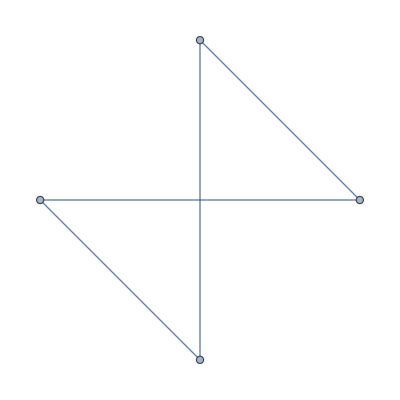

```mathematica
AdjacencyGraph[exampleAdjM]
```

In the textbook, the vertices for this graph were labeled as letters rather than numbers. The AdjacencyGraph function accepts a list of names for the vertices as an optional first argument. It also accepts the usual graph options.

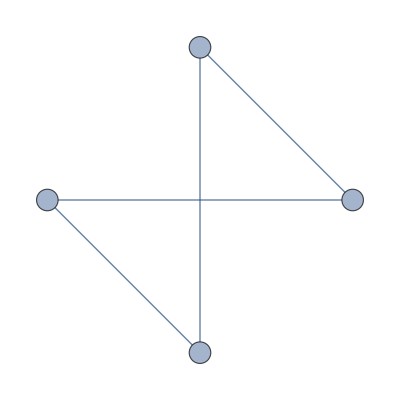

```mathematica
AdjacencyGraph[{"a","b","c","d"},exampleAdjM,VertexLabels->Placed["Name",Center],VertexSize->Small]
```

Notice that this is the same graph as is produced in the textbook, with the exception of the locations of the vertices.

The Wolfram Language also provides a function, AdjacencyMatrix, for computing the adjacency matrix of a graph. The output of this function is always a SparseArray object, which is more efficient at storing large arrays with many entries 0. You can display a SparseArray with MatrixForm, as usual, and you can convert it into the usual list of lists representation with the function Normal.

```mathematica
wheelAdjacency=AdjacencyMatrix[WheelGraph[7]]
```

SparseArray[…]

```mathematica
wheelAdjacency//MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0)

```mathematica
wheelAdjacency//Normal
```

{{0,1,1,1,1,1,1},{1,0,1,0,0,0,1},{1,1,0,1,0,0,0},{1,0,1,0,1,0,0},{1,0,0,1,0,1,0},{1,0,0,0,1,0,1},{1,1,0,0,0,1,0}}

### Adjacency Lists

Recall that a representation of a graph as an adjacency list consists of the lists of neighbors of each vertex.

Earlier, we saw the function AdjacencyList used to determine the list of vertices adjacent to a given vertex. For example, the following determines the vertices adjacent to vertex 2 in the wheel graph on 7 vertices.

```mathematica
AdjacencyList[WheelGraph[7],2]
```

{1,3,7}

By looping over the vertex set, we create a function that returns an Association containing the adjacency lists. Note that applying Dataset to a single Association, displays a table with the rows labeled by the keys.

```mathematica
adjacencyList[G_Graph]:=Association@@Table[v->AdjacencyList[G,v],{v,VertexList[G]}]
```

```mathematica
adjacencyList[WheelGraph[7]]//Dataset
```

Dataset[<>]

The Wolfram Language does not include a function to create a graph from an adjacency list. However, it is not difficult to create a function that transforms an adjacency list into a graph object. We will use the adjacency matrix as an intermediate in order to illustrate how to build a matrix as a SparseArray. We will create a function adjacencyListGraph that accepts as its argument an Association whose keys are the vertices and with the lists of adjacent vertices as the corresponding values. We will assume that the graph does not contain multiple edges.

Our first step is to define a predicate that checks that the rules making up the association are of the correct form. Specifically, each rule in an association representing an adjacency list for a graph can have any object as the left-hand element, but the right-hand element must be a list.

```mathematica
adjacencyRuleQ[r_Rule]:=ListQ[r[[2]]]
```

With this predicate in place, the signature of our function will be:

```mathematica
adjacencyListGraph[A:Association[__?adjacencyRuleQ]]:=
```

This will ensure that the argument is an Association representing an adjacency list of a graph.

The main work of the function will be to transform the list into a matrix with 1s in the locations specified by the adjacency list. We mentioned above that a SparseArray is particularly suitable for matrices with few non-zero entries. To further explore this type of object, we will have our adjacencyListGraph function create a SparseArray as part of its operation. There are several different syntax options for creating a SparseArray, but we will use the most descriptive: a list of rules identifying positions with values. For example, to create a 4×4 matrix with 1s in positions (1,3), (2,4), and (4,1), you enter the following.

```mathematica
SparseArray[{{1,3}->1,{2,4}->1,{4,1}->1},{4,4}]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

Observe that the first argument is a list of rules with the positions within the matrix given as lists on the left hand of each rule, and the value that belongs in the position on the right. The second argument to SparseArray is a list specifying the dimensions of the matrix. If the second argument is omitted, the Wolfram Language will attempt to deduce the size of the matrix from the given entries.

The adjacencyListGraph function will begin by determining the vertex set of the graph. Consider the example adjacency list shown below.

```mathematica
exampleList=<|"a"->{"b","c",3},"b"->{"c"},"c"->{3}|>
```

<|a→{b,c,3},b→{c},c→{3}|>

Note that the vertices are not of all the same type—three are strings and another an integer. Also note that one of the vertices does not appear as a key. While a properly formed adjacency list would include the rule 3 → {}, we will design our function to be sufficiently robust to handle such input. We use Keys and Values to extract the keys and values. The result of Values is a list of lists and so will need to be flattened.

```mathematica
exampleListVertices=Union[Keys[exampleList],Flatten@Values[exampleList]]
```

{3,a,b,c}

In order to create an adjacency matrix, we need to translate the names of the vertices into positions. We will create an Association with the vertex names as keys and their positions in the list of vertices as the values. The MapThread function will accept a function of multiple arguments and a list of lists. The result will be a list in which each element will be the function applied to the elements in the corresponding positions. This is illustrated below with a undefined symbol in the first argument.

```mathematica
MapThread[f,{{1,2,3},{"a","b","c"}}]
```

{f[1,a],f[2,b],f[3,c]}

This allows us to create a list of rules identifying the names of vertices with their position in the list.

```mathematica
exampleDictionary=Association[MapThread[Rule,{exampleListVertices,Range[4]}]]
```

<|3→1,a→2,b→3,c→4|>

With this association in place, we can access the position of a vertex as follows:

```mathematica
exampleDictionary["a"]
```

2

To build the rules that define the SparseArray, we use Table with two table variables—first looping over the keys of the association and then over the lists of vertices adjacent to them.

```mathematica
Table[{exampleDictionary[v],exampleDictionary[w]}->1,{v,Keys[exampleList]},{w,exampleList[v]}]
```

{{{2,3}→1,{2,4}→1,{2,1}→1},{{3,4}→1},{{4,1}→1}}

This will need to be flattened in order to serve as the argument of SparseArray.

```mathematica
SparseArray[Flatten[Table[{exampleDictionary[v],exampleDictionary[w]}->1,{v,Keys[exampleList]},{w,exampleList[v]}]]]//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 1 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

We now build adjacencyListGraph. We use a BlankNullSequence (___), which matches any number of argument, including 0, to pass options from this function to AdjacencyGraph.

```mathematica
adjacencyListGraph[A:Association[__?adjacencyRuleQ],opts___]:=Module[{V,n,D,rules,v,w},
V=Union[Keys[A],Flatten@Values[A]];
n=Length[V];
D=Association[MapThread[Rule,{V,Range[n]}]];
rules=Flatten[Table[{D[v],D[w]}->1,{v,Keys[A]},{w,A[v]}]];
AdjacencyGraph[SparseArray[rules,{n,n}],opts]
]
```

We apply this function to an example.

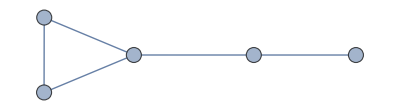

```mathematica
exampleAL=adjacencyListGraph[<|1->{2,3},2->{1,3,4},3->{1,2},4->{2,5},5->{4}|>,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

### Incidence Matrices

The third representation of graphs that we are considering is the incidence matrix. For a graph G with n vertices and m edges, the associated incidence matrix is the n×m matrix whose (i,j) entry is 1 if vertex i is an endpoint of edge j, and 0 otherwise.

The Wolfram Language includes functions for working with incidence matrices. Given an incidence matrix M, the function IncidenceGraph will produce the associated graph. As an example, we reverse Example 6 from Section 10.3 and use the incidence matrix given in the solution in order to reproduce the graph.

```mathematica
exampleIncidenceM={{1,1,0,0,0,0},{0,0,1,1,0,1},{0,0,0,0,1,1},{1,0,1,0,0,0},{0,1,0,1,1,0}};
exampleIncidenceM//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0)

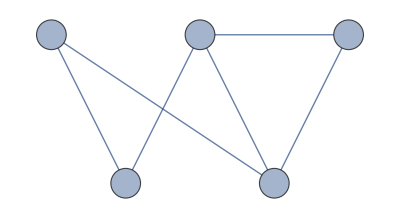

```mathematica
exampleIncidenceG=IncidenceGraph[exampleIncidenceM,VertexLabels->Placed["Name",Center,Subscript[v, #]&],VertexSize->Medium,VertexCoordinates->{{0,1},{1,1},{2,1},{0.5,0},{1.5,0}}]
```

Note that, in order to label the vertices with subscripted v’s, we use Placed with a function as the third argument. This function applies to the label determined by the first argument to produce the displayed label. So these vertices are named 1 through 6 and those names become subscripts in their labels.

For the reverse, the IncidenceMatrix function will produce the incidence matrix for a Graph object. We apply this function to the previous graph. The output from this function is a SparseArray object, so we apply MatrixForm to view it.

```mathematica
IncidenceMatrix[exampleIncidenceG]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0)

For a directed graph, the IncidenceMatrix function returns a matrix with a 1 in position (i,j) indicating that the vertex i is the head of edge j and an entry of -1 indicating that the vertex is the tail of the edge.

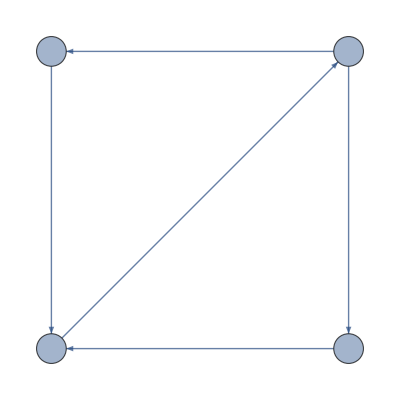

```mathematica
directedIncidenceG=Graph[{1->2,2->3,3->1,2->4,4->1},DirectedEdges->True,VertexLabels->Placed["Name",Center],VertexSize->Small,VertexCoordinates->{{0,0},{1,1},{0,1},{1,0}}]
```

```mathematica
IncidenceMatrix[directedIncidenceG]//MatrixForm
```

(-1 | 0 | 1 | 0 | 1
1 | -1 | 0 | -1 | 0
0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 1 | -1)

### Isomorphism of Graphs

We conclude Section 10.3 with a brief discussion of isomorphism of graphs and graph invariants. Determining whether two graphs are isomorphic is a difficult problem. The naive approach (exhaustively checking each possible mapping) can require exponential time.

Graph invariants are useful tools for confirming that two graphs are not isomorphic. While there is no complete collection of graph invariants that will definitively conclude whether two graphs are or are not isomorphic, they can, for many pairs of graphs, quickly demonstrate the impossibility of an isomorphism. We will create a function that will check some of the basic invariants: number of vertices, number of edges, whether the graph is directed, and whether it is bipartite. We also introduce another invariant: the degree sequence.

For a graph G, the degree sequence is the list of the degrees of the vertices of the graph sorted in ascending order. The Wolfram Language function VertexDegree applied to a graph and a vertex returns the degree of the vertex. Applied to the graph with no second argument, it produces a list of the degrees of the vertices of a graph, listed in order of the vertices. Since this depends on the order in which Mathematica stores the vertices, it is not an invariant. However, applying the Sort function to the result of VertexDegree returns the degree sequence for the graph, which is an invariant.

The function defined below checks, one at a time, the invariants we have mentioned. If any of the invariants indicate that the graphs are not isomorphic, the procedure prints a statement to that effect.

```mathematica
checkInvariants[G1_Graph,G2_Graph]:=Module[{notIsomorphic=False},
If[VertexCount[G1]≠VertexCount[G2],
notIsomorphic=True;
Print["Different numbers of vertices."]
];
If[EdgeCount[G1]≠EdgeCount[G2],
notIsomorphic=True;
Print["Different numbers of edges."]
];
If[!Equivalent[DirectedGraphQ[G1],DirectedGraphQ[G2]],
notIsomorphic=True;
Print["One is directed, one is undirected."]
];
If[!Equivalent[BipartiteGraphQ[G1],BipartiteGraphQ[G2]],
notIsomorphic=True;
Print["One is bipartite, one is not."]
];
If[Sort[VertexDegree[G1]]≠Sort[VertexDegree[G2]],
notIsomorphic=True;
Print["Degree sequences do not match."]
];
If[notIsomorphic,
Print["The graphs are not isomorphic."],
Print["The graphs MAY be isomorphic."]
]
]
```

```mathematica
checkInvariants[directedIncidenceG,exampleIncidenceG]
```

Different numbers of vertices.

Different numbers of edges.

One is directed, one is undirected.

Degree sequences do not match.

The graphs are not isomorphic.

```mathematica
checkInvariants[CompleteGraph[3],CycleGraph[3]]
```

The graphs MAY be isomorphic.

The Wolfram Language provides a function, IsomorphicGraphQ, for determining whether or not two graphs are isomorphic. This function applies to any Graph object. The IsomorphicGraphQ function accepts two graphs as its arguments. It returns True if the graphs are isomorphic.

```mathematica
IsomorphicGraphQ[CompleteGraph[3],CycleGraph[3]]
```

True

The FindGraphIsomorphism function can be used to determine an explicit isomorphism for a pair of graphs that are in fact isomorphic. Like IsomorphicGraphQ, the only required arguments are the two graphs, although you can give a positive integer or the symbol All as the third argument in order to attempt to produce multiple isomorphisms. If the two graphs are in fact isomorphic, the output is a list of associations composed of rules of the form v→w indicating that vertex v in the first graph is mapped to vertex w in the second graph. If the graphs are not isomorphic, IsomorphicGraphQ returns an empty list.

We illustrate by reproducing the graphs in Figure 12 of Section 10.3 of the textbook.

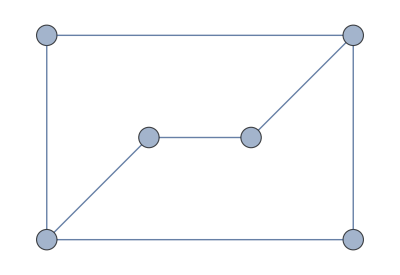

```mathematica
figure12G=Graph[{1,2,3,4,5,6},{1->2,1->4,2->3,2->6,3->4,4->5,5->6},DirectedEdges->False,VertexLabels->Placed["Name",Center,Subscript[u, #]&],VertexSize->Medium,VertexCoordinates->{{0,2},{3,2},{3,0},{0,0},{1,1},{2,1}}]
```

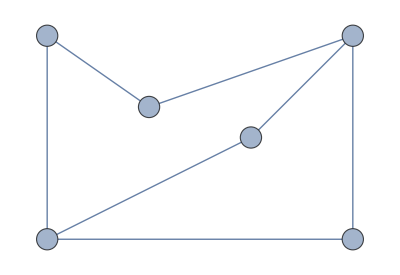

```mathematica
figure12H=Graph[{1,2,3,4,5,6},{1->2,1->5,2->3,3->4,3->6,4->5,5->6},DirectedEdges->False,VertexLabels->Placed["Name",Center,Subscript[v, #]&],VertexSize->Medium,VertexCoordinates->{{0,2},{1,1.3},{3,2},{3,0},{0,0},{2,1}}]
```

Applying IsomorphicGraphQ confirms that the graphs are isomorphic.

```mathematica
IsomorphicGraphQ[figure12G,figure12H]
```

True

FindGraphIsomorphism determines the isomorphism.

```mathematica
FindGraphIsomorphism[figure12G,figure12H]
```

{<|1→4,2→3,3→6,4→5,5→1,6→2|>}

Observe that there are four different isomorphisms.

```mathematica
FindGraphIsomorphism[figure12G,figure12H,All]
```

{<|1→4,2→3,3→6,4→5,5→1,6→2|>,<|1→4,2→5,3→6,4→3,5→2,6→1|>,<|1→6,2→3,3→4,4→5,5→1,6→2|>,<|1→6,2→5,3→4,4→3,5→2,6→1|>}

We can make an isomorphism visible by coloring each vertex in the second graph and using the composition to then determine colors for the first graph. To choose the colors, we’ll make use of the Wolfram Language built-in color schemes. There are a number of different ways to use ColorData; we will simply use the indexed color schemes. If you apply ColorData to a positive integer up to 113, the result is a ColorDataFunction, which is a function that returns a color.

```mathematica
ColorData[10][3]
```

RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217]

Passing ColorData the second argument “Panel” (including the quotation marks) will display the colors produced by the particular ColorDataFunction.

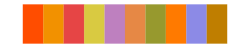

```mathematica
ColorData[87,"Panel"]
```

Provided the ColorDataFunction has enough colors, we can shade all of the vertices of a graph with different colors by forming a list of rules.

```mathematica
Table[v->ColorData[10][v],{v,6}]
```

{1→RGBColor[0.6980392156862745, 0.01568627450980392, 0.],2→RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],3→RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],4→RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],5→RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],6→RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196]}

This list will be the value of VertexStyle. Here is the graph H with colors added

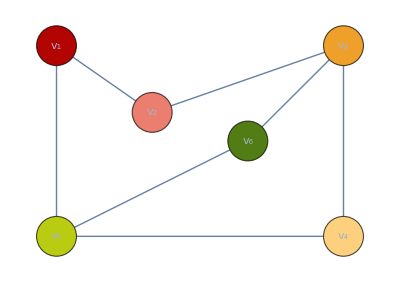

```mathematica
figure12Hcolor=Graph[{1,2,3,4,5,6},{1->2,1->5,2->3,3->4,3->6,4->5,5->6},DirectedEdges->False,VertexLabels->Placed["Name",Center,Subscript[v, #]&],VertexSize->Large,VertexStyle->Table[v->ColorData[10][v],{v,6}],VertexCoordinates->{{0,2},{1,1.3},{3,2},{3,0},{0,0},{2,1}}]
```

We then color G by applying one of the isomorphisms before accessing the color.

```mathematica
figure12isomorphism=FindGraphIsomorphism[figure12G,figure12H,All][[1]]
```

<|1→4,2→3,3→6,4→5,5→1,6→2|>

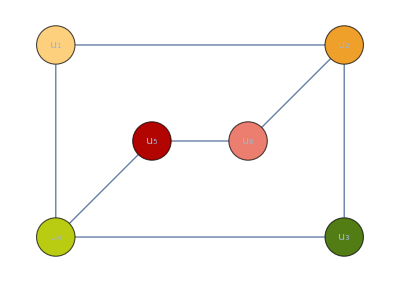

```mathematica
figure12Gcolor=Graph[{1,2,3,4,5,6},{1->2,1->4,2->3,2->6,3->4,4->5,5->6},DirectedEdges->False,VertexLabels->Placed["Name",Center,Subscript[u, #]&],VertexSize->Large,VertexStyle->Table[v->ColorData[10][figure12isomorphism[v]],{v,6}],VertexCoordinates->{{0,2},{3,2},{3,0},{0,0},{1,1},{2,1}}]
```

We put them side-by-side to compare with GraphicsRow, which like Row for more general display, takes a list of objects and displays them in a row.

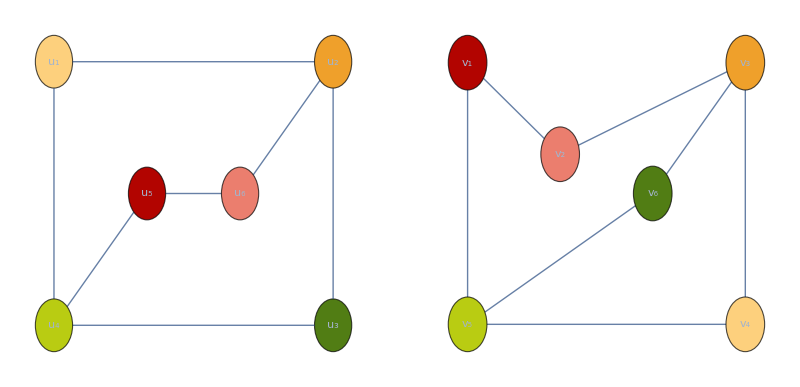

```mathematica
GraphicsRow[{figure12Gcolor,figure12Hcolor}]
```

## 10.4 Connectivity

The Wolfram Language provides a number of functions related to connectivity of graphs.

The first such function that we consider is ConnectedGraphQ. This function takes one argument, the name of the graph, and returns true or false. As an example, consider the complete bipartite graph K_(2,3) and its complement.

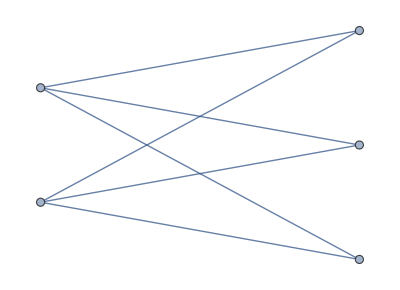

```mathematica
CompleteGraph[{2,3}]
```

```mathematica
ConnectedGraphQ[CompleteGraph[{2,3}]]
```

True

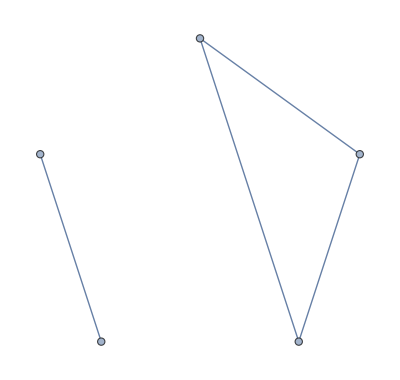

```mathematica
GraphComplement[CompleteGraph[{2,3}]]
```

```mathematica
ConnectedGraphQ[GraphComplement[CompleteGraph[{2,3}]]]
```

False

When used with a directed graph, ConnectedGraphQ returns True if the directed graph is strongly connected.

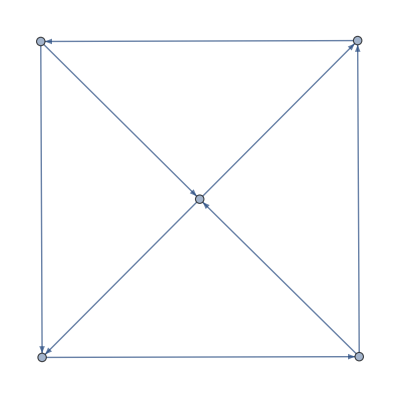

```mathematica
stronglyConnectedEx=Graph[{1->2,2->3,3->4,4->1,1->5,5->2,3->5,5->4}]
```

Applying ConnectedGraphQ reveals that the above graph is connected.

```mathematica
ConnectedGraphQ[stronglyConnectedEx]
```

True

The following example, while weakly connected, is not strongly connected and thus ConnectedGraphQ will return False.

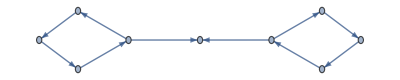

```mathematica
weaklyConnectedEx=Graph[{4->2,2->1,1->3,3->4,4->5,6->8,8->9,9->7,7->6,6->5}]
```

```mathematica
ConnectedGraphQ[weaklyConnectedEx]
```

False

The WeaklyConnectedGraphQ function will determine whether a directed graph is weakly connected. A graph is weakly connected if it is connected as an undirected graph.

```mathematica
WeaklyConnectedGraphQ[weaklyConnectedEx]
```

True

The Wolfram Language also has functions to extract the connected components of a graph that is not connected. The ConnectedComponents function takes a graph as input and returns a list of lists of vertices.

As an example, consider the complement of the graph K_(2,3).

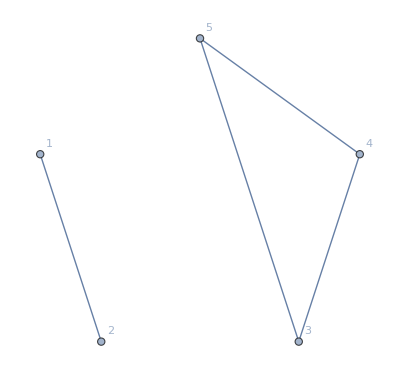

```mathematica
GraphComplement[CompleteGraph[{2,3}],VertexLabels->"Name"]
```

```mathematica
ConnectedComponents[GraphComplement[CompleteGraph[{2,3}]]]
```

{{3,4,5},{1,2}}

This output indicates that the complement of K_(2,3) has two connected components, one with vertex set {1,2} and the other with vertex set {3,4,5}.

For directed graphs, ConnectedComponents will produce the strongly connected components. The WeaklyConnectedComponents function will output the weakly connected components.

```mathematica
ConnectedComponents[weaklyConnectedEx]
```

{{5},{4,2,1,3},{6,8,9,7}}

```mathematica
WeaklyConnectedComponents[weaklyConnectedEx]
```

{{4,2,1,3,5,6,8,9,7}}

### Coloring the Components

We now present a function that will color code the connected components in a graph. (This function will color up to ten components before repeating colors.)

As in the previous section, we use ColorData to obtain the colors. Also note the use of PropertyValue to set the VertexStyle property. We first saw PropertyValue in the subsection on edge contraction in Section 10.2 of this manual. Finally, note the use of Mod with third argument 1, which causes the result of Mod to have minimum value 1. This allows us to cycle through the list of ten colors provided by the particular ColorDataFunction we chose.

```mathematica
highlightComponents[G_Graph,opts___]:=Module[{components,c,i,v,H=G},
components=ConnectedComponents[G];
c=0;
For[i=1,i≤Length[components],i++,
c=Mod[c+1,10,1];
Do[PropertyValue[{H,v},VertexStyle]=ColorData[14][c]
,{v,components[[i]]}]
];
Graph[H,opts]
]
```

We apply this function to the weakly connected graph above.

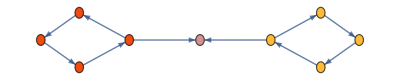

```mathematica
highlightComponents[weaklyConnectedEx,VertexSize->Medium]
```

### Counting Paths Between Vertices

The last topic that we consider in this section is determining the number of paths between two vertices of a given length. As described in the textbook, if A is the adjacency matrix for a graph (which may be undirected or directed and may include loops and multiple edges), then the (i,j) entry of the matrix A^r is the number of paths of length r from vertex i to vertex j.

As an example, consider the stronglyConnectedEx graph from above. We can obtain its adjacency matrix by applying the AdjacencyMatrix function to the name of the graph.

```mathematica
aMatrix=AdjacencyMatrix[stronglyConnectedEx];
aMatrix//MatrixForm
```

(0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0)

Recall that AdjacencyMatrix produces a SparseArray. You could use Normal to transform the SparseArray object into a usual list of lists representation of the matrix. However, Mathematica can compute more efficiently with the SparseArray.

Next, compute some powers of the adjacency matrix.

```mathematica
Table[MatrixForm[MatrixPower[aMatrix,i]],{i,2,7}]
```

{(0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0),(1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0
0 | 1 | 0 | 1 | 2),(1 | 2 | 0 | 2 | 2
1 | 1 | 1 | 0 | 1
0 | 2 | 1 | 2 | 2
1 | 0 | 1 | 1 | 1
1 | 2 | 1 | 2 | 0),(2 | 3 | 2 | 2 | 1
0 | 2 | 1 | 2 | 2
2 | 2 | 2 | 3 | 1
1 | 2 | 0 | 2 | 2
2 | 1 | 2 | 1 | 2),(2 | 3 | 3 | 3 | 4
2 | 2 | 2 | 3 | 1
3 | 3 | 2 | 3 | 4
2 | 3 | 2 | 2 | 1
1 | 4 | 1 | 4 | 4),(3 | 6 | 3 | 7 | 5
3 | 3 | 2 | 3 | 4
3 | 7 | 3 | 6 | 5
2 | 3 | 3 | 3 | 4
4 | 5 | 4 | 5 | 2)}

Note that the MatrixPower function is used to compute powers of matrices. Using the Power (^) operator on a matrix computes element-wise.

We see that there are 4 paths of length 6 from vertex 3 to vertex 5, since the (3,5) entry in the 6th power of the adjacency matrix is 4. We also see that there are cycles of length 3 for every vertex and there are no cycles of length less than 3. Finally, we know that the shortest path from vertex 2 to vertex 1 is of length 3, since the (2,1) entry is 0 for the first and second powers of the matrix.

## 10.5 Euler and Hamilton Paths

In this section, we will show how to use Mathematica to solve two problems that seem closely related, but which are quite different in computational complexity. The two problems that will be analyzed are the problem of finding a simple circuit that contains every edge exactly once (an Euler circuit) and the problem of finding a simple circuit that contains every vertex exactly once (a Hamilton circuit). (Note that the textbook uses the term circuit while the Wolfram Language uses the word cycle. These two terms are synonymous.)

### Euler Circuits

The Wolfram Language comes equipped with a function to determine if a given simple graph has an Euler circuit or not. This function, EulerianGraphQ, takes one argument, a Graph object. As an example, we have Mathematica check to see if K_5 is Eulerian, that is, has an Euler circuit.

```mathematica
EulerianGraphQ[CompleteGraph[5]]
```

True

To explicitly find an Euler circuit, we use the function FindEulerianCycle. The function accepts one or two arguments. The first argument should be a graph, although you can provide a list of rules specifying the edges rather than a Graph object. If the graph is the only argument, the function returns a list containing a single list of edges representing an Euler circuit. For example, the following identifies an Euler circuit on the complete graph K_5.

```mathematica
FindEulerianCycle[CompleteGraph[5]]
```

{{1<->5,5<->4,4<->3,3<->5,5<->2,2<->4,4<->1,1<->3,3<->2,2<->1}}

If you provide FindEulerianCycle with a positive integer as a second argument, Mathematica will attempt to find more than one Euler circuit, with the integer serving as a maximum number of cycles to return, provided they exist. In this case, the output will be a list of lists of edges, with each sublist representing a distinct circuit.

```mathematica
FindEulerianCycle[CompleteGraph[5],3]
```

{{1<->2,2<->5,5<->4,4<->3,3<->5,5<->1,1<->4,4<->2,2<->3,3<->1},{1<->2,2<->5,5<->4,4<->3,3<->5,5<->1,1<->3,3<->2,2<->4,4<->1},{1<->2,2<->5,5<->4,4<->3,3<->2,2<->4,4<->1,1<->5,5<->3,3<->1}}

With the symbol All as the second argument, Mathematica will determine all of the Euler circuits. We see below that the complete graph on 5 vertices has 132 Euler circuits.

```mathematica
Length[FindEulerianCycle[CompleteGraph[5],All]]
```

132

Now, we will visualize this path by creating an animation that successively highlights the edges in the path. To do this we will use the Animate function. The Animate function takes two arguments, similar to Table. The first argument is a Wolfram Language expression, typically one that generates an image and that is dependent on a variable. The second argument is a list describing the range of the variable. The structure of this list is similar to the second argument in a Table.

We will also be making use of two options. Setting the AnimationRunning option to False will prevent the animation from beginning until you explicitly click on the play button. Without this option, the animation would run as soon as Mathematica has finished generating it. Setting the AnimationRepetitions option to 1 will cause the animation to stop once it has played through. This option defaults to Infinity, meaning it will automatically restart every time it reaches the end.

To create the animation, we need a graph and a circuit. We will use K_5 as the graph and we store the circuit as exampleCircuit. Note that we apply First since FindEulerianCycle returns a list of lists.

```mathematica
exampleCircuit=First[FindEulerianCycle[CompleteGraph[5]]]
```

{1<->5,5<->4,4<->3,3<->5,5<->2,2<->4,4<->1,1<->3,3<->2,2<->1}

To display the path, we will apply the HighlightGraph function. This function was first described in Section 10.2 in the section on bipartite graphs. It takes two arguments: a graph and a list containing vertices, edges, or subgraphs.

To draw the successive stages in the circuit, we will apply HighlightGraph to the graph and to a sublist of exampleCircuit. We will obtain the sublist by applying Part ([[…]]) to a Span (;;) from 1 to the current stage. For example, to display the path after three steps, we enter the following:

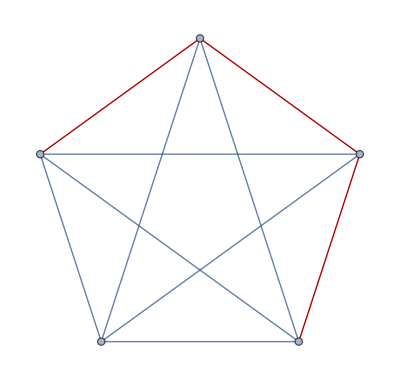

```mathematica
HighlightGraph[CompleteGraph[5],exampleCircuit[[1;;3]]]
```

Note that the span from 1 to 0 will result in the empty list and thus nothing highlighted.

```mathematica
exampleCircuit[[1;;0]]
```

{}

```mathematica
HighlightGraph[CompleteGraph[5],exampleCircuit[[1;;0]]]
```

-Graphics-

We produce the animation using HighlightGraph as above, with the second argument to the Span (;;) as a variable. In the second argument of Animate, this variable will be set to run from 0 to the Length of the path. Note that, unlike Table, the variables in an Animate are not assumed to be restricted to integers, so we must specify a step value of 1 in the variable specification.

```mathematica
Animate[HighlightGraph[CompleteGraph[5],exampleCircuit[[1;;i]]],{i,0,Length[exampleCircuit],1},AnimationRunning->False,AnimationRepetitions->1]
```

We now turn this into a function. The only difference between the animatePath function below and the example from above is that we replace the variable in the loop specification with the list {i, 0, "step"}. This syntax gives the variable i the initial value 0 and labels it as “step” in the animation controller.

```mathematica
animatePath[g_Graph,p_List]:=Module[{i,len},
len=Length[p];
Animate[HighlightGraph[g,p[[1;;i]]],{{i,0,"step"},0,len,1},AnimationRunning->False,AnimationRepetitions->1]
]
```

To use this function, we just pass it an Eulerian graph, a circuit, and any options for drawing the graph.

```mathematica
animatePath[CompleteGraph[7,VertexSize->Medium,VertexLabels->Placed["Name",Center]],First[FindEulerianCycle[CompleteGraph[7]]]]
```

You can see the Euler circuit traced out by clicking on the play button.

Note that while our examples have all been undirected, the functions described here also apply to directed graphs, multigraphs, etc. Here, for example, is the bridges of Königsberg graph.

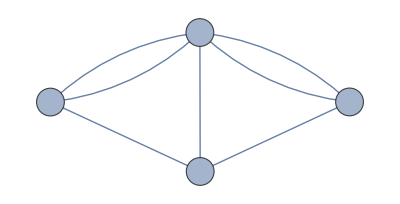

```mathematica
konigsberg=Graph[{"A"->"B","A"->"B","A"->"C","A"->"C","A"->"D","B"->"D","C"->"D"},DirectedEdges->False,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

```mathematica
EulerianGraphQ[konigsberg]
```

False

### Euler Paths

While the Wolfram Language’s includes a built-in function for finding Eulerian circuits, it does not have a function for finding Eulerian paths that are not circuits. Moreover, building a function for finding Euler paths from scratch can be helpful in understanding the algorithm for finding both paths and circuits. We know, from Theorem 1 of Section 10.5, that a connected multigraph with at least two vertices has an Euler circuit if and only if the degree of every vertex is even. We also know, from Theorem 2, that if the graph has exactly two vertices of odd degree, then there is a Euler path which is not a circuit.

Using this fact, we can write a simple function for determining whether or not an undirected pseudograph (multiple edges and loops allowed) has an Euler path. The function first uses the Wolfram Language built-in functions to confirm that the graph given as the argument is undirected and connected. It uses VertexDegree to obtain the list of the degrees of the vertices in the graph. We then Map (/@) the EvenQ predicate over the list to transform the list of degrees into a list of true and false. Finally, we Count those that are false and check whether that number, that is, the number of vertices of odd degree, is 0 or 2. We include 0, since an Euler circuit is a path. Note that MemberQ determines whether the second argument is a member of the first argument.

```mathematica
eulerPathQ[g_Graph]:=UndirectedGraphQ[g]&&ConnectedGraphQ[g]&&MemberQ[{0,2},Count[EvenQ/@VertexDegree[g],False]]
```

Consider the graph G_2 from Example 4, which has an Euler path, but not a circuit.

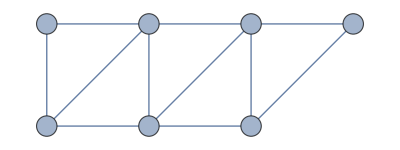

```mathematica
figure7G2=Graph[{"a","g","f","e","b","c","d"},{"a"->"g","a"->"b","b"->"c","b"->"g","c"->"d","c"->"g","c"->"f","d"->"e","d"->"f","e"->"f","f"->"g"},DirectedEdges->False,
VertexLabels->Placed["Name",Center],VertexSize->Medium,
VertexCoordinates->{{0,1},{1,1},{2,1},{3,1},{0,0},{1,0},{2,0}}]
```

```mathematica
EulerianGraphQ[figure7G2]
```

False

```mathematica
eulerPathQ[figure7G2]
```

True

Now that we have a test that tells us if a path exists, we modify Algorithm 1 from Section 10.5 in order to find an Euler path, if it exists. The difference between this function and Algorithm 1 is that, if there is not an Euler circuit, we need to be sure to begin at one of the vertices of odd degree and end at the other. To do this, we begin by creating a new graph with an additional vertex adjacent to the two vertices of odd degree. We then follow Algorithm 1 to build an Euler circuit, and then cut out the temporary vertex.

```mathematica
findEulerianPath[g_Graph]:=Module[{H,pathQ,oddvertices,newvertex,circuit,subC,i,n,v,insertPoint,w,buildingSub,oldC,newVlocations},
If[!eulerPathQ[g],Return[$Failed]];
circuit={};
H=g;
If[Count[EvenQ/@VertexDegree[g],False]==2,
pathQ=True;
oddvertices=Select[VertexList[g],OddQ[VertexDegree[g,#]]&];
H=VertexAdd[H,newvertex];
H=EdgeAdd[H,{newvertex->oddvertices[[1]],newvertex->oddvertices[[2]]}],
pathQ=False
];
While[EdgeList[H]≠{},
(* find a starting point *)
If[circuit=={},
subC={EdgeList[H][[1]]};
H=EdgeDelete[H,subC[[1]]];
insertPoint=0,
For[i=1,i≤Length[circuit],i++,
v=circuit[[i,2]];
n=neighbors[H,v];
If[n≠{},
w=n[[1]];
subC={v->w};
insertPoint=i;
H=EdgeDelete[H,UndirectedEdge[v,w]];
Break[]
]
]
];
(* build a subcircuit *)
buildingSub=True;
While[buildingSub&&EdgeList[H]≠{},
v=subC[[-1,2]];
w=First[neighbors[H,v]];
H=EdgeDelete[H,UndirectedEdge[v,w]];
AppendTo[subC,UndirectedEdge[v,w]];
If[w==subC[[1,1]],buildingSub=False]
];
(* splice the subcircuit into the main circuit *)
If[circuit=={},
circuit=subC,
circuit=Flatten[Insert[circuit,subC,insertPoint+1]]
]
];
If[pathQ,
newVlocations=Position[circuit,newvertex][[All,1]];
Join[circuit[[Max[newVlocations]+1;;-1]],circuit[[1;;Min[newVlocations]-1]]],
circuit
]
]
```

The function begins with a use of eulerPathQ in order to avoid searching for a path that cannot exist. It then assigns to the symbol H a copy of the graph. It is this copy that is used throughout the rest of the function, rather than the input that was passed to the algorithm. The benefit of using a copy is that the function will be able to manipulate it as the algorithm proceeds, for example, by deleting edges of H once they are included in the circuit so that those edges are not reused.

After copying the input graph, the function tests to see whether it has two vertices of odd degree. If it does, then the graph H is modified to include a new vertex and edges between this new vertex and the two with odd degree. The result is that H has vertices of all even degree, and thus an Euler circuit must exist. Note that the symbol used for the name of the new vertex is localized to the module. This means that, in practice, the symbol actually being used is something along the lines of newvertex$371, so it is unlikely to already exist in the graph. The function also sets a flag, pathQ, to true or false, depending on whether the graph has a path or circuit.

Once H has been modified, if needed, the function follows Algorithm 1 from Section 10.5. There are two key ideas at the heart of this algorithm. The first is that, for a graph whose vertices all have even degree, if you pick any vertex to start at and follow edges at random but without repetition, you will definitely return to the original vertex and create a circuit. The second key idea is that (for a connected graph), if your circuit does not include all of the edges of the graph, then some vertex used in the existing circuit can be made the starting point for a new subcircuit. This subcircuit can then be spliced into the main circuit. This will eventually use all the edges and the result will be a Euler circuit.

The symbol circuit will hold the main circuit that the function finds in H. The circuit will be stored as a list of the edges through which the circuit passes and is initialized to the empty list. The main While loop consists of three parts: (1) determining the starting point for the subcircuit (named subC); (2) building the subcircuit; and (3) splicing the subcircuit into the main circuit.

The first step, finding the starting point for the subcircuit, depends on the state of the main circuit. If circuit is the empty list (i.e., this is the first pass through the main loop), then the starting point is the first edge in the graph. If the main circuit is not empty, then the else clause looks at the vertices in the main circuit to find one that has neighbors (since edges are deleted from H as they are added to the circuit, only vertices that are an endpoint of an unused edge have neighbors). The first vertex that has a neighbor is used as the starting point for the subcircuit. The insertPoint variable is used to keep track of the index, relative to circuit, of the starting vertex for the subcircuit. This is used when the subcircuit is spliced into the main circuit.

The second step is to build subC. The buildingSub symbol is used to control the While loop. It is initialized to true and is set to false once subC has returned to its starting vertex and is thus a circuit. The variable v is set to the last vertex currently included as part of the subcircuit and w represents a neighbor of v. To remove the edge between v and w from H, we use EdgeDelete.

After deleting the edge from H, the newest vertex is compared with the starting vertex to determine if the circuit has been closed. If the new vertex closes the circuit, then the buildingSub variable is set to false, which causes the loop to terminate. Otherwise, the While loop continues building the subcircuit.

The third step, once the subcircuit has been built, is to splice it into the main circuit. If circuit is empty, it is merely set to subC. Otherwise, Insert is used to add the subcircuit. Insert takes a list as the first argument and adds the expression given as the second argument in the position specified by the third argument. The elements previously in that position and later and pushed down to make room. We give the third argument as insertPoint+1 to insert the sublist between the edges at position insertPoint and position insertPoint+1.

The main While loop continues until all the edges of the graph have been included in the circuit, making circuit an Euler circuit for H. Then the final step is to either output the circuit, if the original graph has an Euler circuit, or to cut the temporary vertex and corresponding edges out of the circuit and produce the Euler path. For this, we use Position, with first argument a list and second argument a pattern to search for, to find the locations of the temporary vertex in the circuit. The vertex will appear twice and its location will be reported as a pair consisting of the position within circuit and a 1 or 2 corresponding to its location on the edge. The Part specification [[All,1]] returns the first element in all subexpressions and thus extracts the locations of the edges within the circuit list containing the temporary vertex. Once the locations of the temporary vertex have been found, the function uses Join to combine the part of the circuit after it has visited the temporary vertex with the part before. The result is the Euler path beginning at one of the vertices of odd degree and ending at the other.

As an example, consider Exercise 5 from Section 10.5.

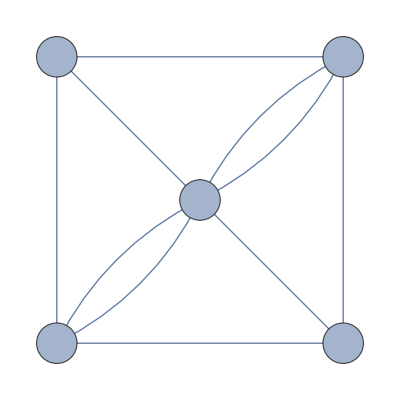

```mathematica
exercise3=Graph[{"a","b","c","d","e"},{"a"->"b","a"->"e","a"->"c","b"->"d","b"->"e","b"->"e","c"->"d","c"->"e","c"->"e","d"->"e"},DirectedEdges->False,VertexSize->Medium,VertexLabels->Placed["Name",Center],
VertexCoordinates->{{0,1},{1,1},{0,0},{1,0},{0.5,0.5}}]
```

```mathematica
exercise3EulerPath=findEulerianPath[exercise3]
```

{d<->e,e<->b,b<->d,d<->c,c<->a,a<->b,b→e,e→c,c<->e,e<->a}

### Hamilton Circuits

Turning our attention to Hamilton circuits, the Wolfram Language provides the function HamiltonianGraphQ for determining whether or not the graph contains a Hamilton circuit. This function, like EulerianGraphQ, accepts a graph as the sole argument. It returns true or false depending on whether the graph has a Hamilton circuit.

```mathematica
hcGraphExample=HypercubeGraph[3]
```

-Graphics-

```mathematica
HamiltonianGraphQ[hcGraphExample]
```

True

The FindHamiltonianCycle function, similar to FindEulerianCycle, accepts a graph as the argument and returns a list containing a Hamiltonian circuit. The optional second argument can be used to find more than one cycle.

```mathematica
FindHamiltonianCycle[hcGraphExample]
```

{{1<->2,2<->4,4<->8,8<->6,6<->5,5<->7,7<->3,3<->1}}

```mathematica
FindHamiltonianCycle[hcGraphExample,All]
```

{{1<->3,3<->7,7<->8,8<->4,4<->2,2<->6,6<->5,5<->1},{1<->3,3<->4,4<->2,2<->6,6<->8,8<->7,7<->5,5<->1},{1<->2,2<->6,6<->8,8<->4,4<->3,3<->7,7<->5,5<->1},{1<->2,2<->4,4<->3,3<->7,7<->8,8<->6,6<->5,5<->1},{1<->2,2<->6,6<->5,5<->7,7<->8,8<->4,4<->3,3<->1},{1<->2,2<->4,4<->8,8<->6,6<->5,5<->7,7<->3,3<->1}}

```mathematica
hcGraphExampleCircuit=First[FindHamiltonianCycle[hcGraphExample]]
```

{1<->2,2<->4,4<->8,8<->6,6<->5,5<->7,7<->3,3<->1}

We can use HighlightGraph to illustrate the path statically.

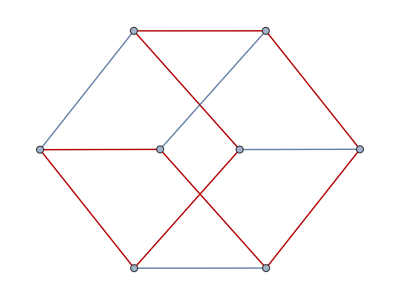

```mathematica
HighlightGraph[hcGraphExample,hcGraphExampleCircuit]
```

Moreover, our animation function animatePath, created above, works equally well here.

```mathematica
animatePath[hcGraphExample,hcGraphExampleCircuit]
```

## 10.6 Shortest-Path Problems

Among the most common problems in graph theory are shortest path problems. Generally, in shortest path problems, we wish to determine a path between two vertices of a weighted graph that is minimal in terms of the total weight of the edges in the path.

To define a Graph object with weighted edges, use the EdgeWeight option. The value associated with the option is the list of the weights of each edge. The weights must appear in the same order as they are displayed in the output by EdgeList. For graphs you define by listing the edges, this is identical to the order you give in the definition.

We reproduce Exercise 2 from Section 10.6 of the textbook to use as an example.

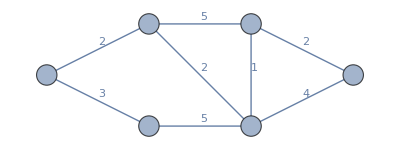

```mathematica
exercise2=Graph[{"a","b","c","d","e","z"},{"a"->"b","a"->"c","b"->"d","b"->"e","c"->"e","d"->"e","d"->"z","e"->"z"},DirectedEdges->False,EdgeWeight->{2,3,5,2,5,1,2,4},VertexCoordinates->{{0,.5},{1,1},{1,0},{2,1},{2,0},{3,.5}},VertexSize->Medium,VertexLabels->Placed["Name",Center],EdgeLabels->Placed["EdgeWeight",{.5,{-1,0}}]]
```

Note the use of the EdgeLabels option to display the edge weights. The second argument of Placed indicates that the label should appear halfway between the vertices and should be shifted to the right. The form of the second argument is {s,{l_x,l_y}}, where s indicates fraction along the edge that the label should appear and {l_x,l_y}, indicates what position within the label is to be located at that position on the line. For example, {0,0} indicates that the lower left corner of the label should appear on the edge, while {-1,0} means that a point to the left of the label should be placed at the edge. You can imagine the label surrounded by a box, and {l_x,l_y} indicates, relative to the lower left corner of that box, where the label should be anchored to the edge. Also, the values are relative to the size of the label, so {-1,0} refers to a point to the left of the label at a distance equal to the width of the label.

A second approach to setting edge weights is by using the EdgeWeight property. Rather than listing all of the edges and then listing the weights separately using the option as shown above, we can wrap the edge definitions in the Property wrapper, setting the edge weights at the same time the edges are described.

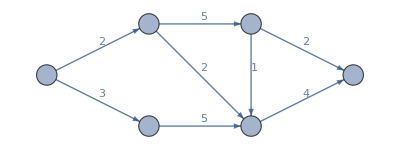

```mathematica
Graph[{"a","b","c","d","e","z"},{Property["a"->"b",EdgeWeight->2],Property["a"->"c",EdgeWeight->3],Property["b"->"d",EdgeWeight->5],Property["b"->"e",EdgeWeight->2],Property["c"->"e",EdgeWeight->5],Property["d"->"e",EdgeWeight->1],Property["d"->"z",EdgeWeight->2],Property["e"->"z",EdgeWeight->4]},VertexCoordinates->{{0,.5},{1,1},{1,0},{2,1},{2,0},{3,.5}},VertexSize->Medium,VertexLabels->Placed["Name",Center],EdgeLabels->Placed["EdgeWeight",{.5,{-1,0}}]]
```

Note in the above that we omitted the DirectedEdges option to illustrate that there is no difference with a directed graph.

You can also define a weighted graph using the WeightedAdjacencyGraph function and an adjacency matrix. Unlike with AdjacencyGraph, the adjacency matrix must use Infinity, or ∞ (EscinfEsc) to indicate that there is no edge between the corresponding vertices. In the example below, we give the list of vertices as the first argument, otherwise Mathematica will automatically use positive integers to name the vertices. Note that WeightedAdjacencyMatrix applied to a weighted graph returns the adjacency matrix with weights.

```mathematica
exercise2matrix={{∞,2,3,∞,∞,∞},{2,∞,∞,5,2,∞},{3,∞,∞,∞,5,∞},{∞,5,∞,∞,1,2},{∞,2,5,1,∞,4},{∞,∞,∞,2,4,∞}};
exercise2matrix//MatrixForm
```

(∞ | 2 | 3 | ∞ | ∞ | ∞
2 | ∞ | ∞ | 5 | 2 | ∞
3 | ∞ | ∞ | ∞ | 5 | ∞
∞ | 5 | ∞ | ∞ | 1 | 2
∞ | 2 | 5 | 1 | ∞ | 4
∞ | ∞ | ∞ | 2 | 4 | ∞)

```mathematica
WeightedAdjacencyGraph[{"a","b","c","d","e","z"},exercise2matrix,VertexCoordinates->{{0,.5},{1,1},{1,0},{2,1},{2,0},{3,.5}},VertexSize->Medium,VertexLabels->Placed["Name",Center],EdgeLabels->Placed["EdgeWeight",{.5,{-1,0}}]]
```

-Graphics-

Now, we will make use of the Wolfram Language’s implementation of path finding algorithms to compute the shortest path between a and z. To do this, we simply call the FindShortestPath function with three arguments: the graph and the names of the starting and ending vertices. The output will be a list of vertices beginning with the starting vertex and ending with the final vertex through which the path runs.

```mathematica
FindShortestPath[exercise2,"a","z"]
```

{a,b,e,d,z}

The PathGraph function can be used to help visualize this path. PathGraph accepts a list of vertices as input and produces the graph obtained by connecting successive vertices with an edge. By default, the graph produced is undirected. To obtain a directed path, assign the DirectedEdges option to True. Here, we will display the path in the graph by applying HighlightGraph, using PathGraph in the second argument.

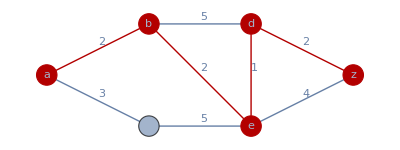

```mathematica
HighlightGraph[exercise2,PathGraph@FindShortestPath[exercise2,"a","z"]]
```

The length of the shortest path can be determined with the GraphDistance function and the same arguments.

```mathematica
GraphDistance[exercise2,"a","z"]
```

7.

If the final argument, the destination vertex, is omitted from GraphDistance, the result will be a list of the lengths of the shortest paths to each vertex of the graph.

```mathematica
GraphDistance[exercise2,"a"]
```

{0,2.,3.,5.,4.,7.}

To determine the shortest path from every vertex to every other vertex, use the GraphDistanceMatrix function. Algorithm 2 in the Exercises of Section 10.6 describes the Floyd–Warshall algorithm (also known as simply the Floyd algorithm), which is one method for computing this matrix.

```mathematica
GraphDistanceMatrix[exercise2]//MatrixForm
```

(0. | 2. | 3. | 5. | 4. | 7.
2. | 0. | 5. | 3. | 2. | 5.
3. | 5. | 0. | 6. | 5. | 8.
5. | 3. | 6. | 0. | 1. | 2.
4. | 2. | 5. | 1. | 0. | 3.
7. | 5. | 8. | 2. | 3. | 0.)

## 10.7 Planar Graphs

This section explains how Mathematica can be used to explore the question of whether a graph is planar by manipulating graphs in order to produce homeomorphic graphs and applying Kuratowski’s Theorem. We consider only undirected simple graphs in this section. The question of planarity for a directed graph can be answered by considering the underlying undirected graph, which can be obtained by applying the function UndirectedGraph.

Before looking at how Mathematica can help you manipulate graphs to apply Kuratowski’s theorem manually, note that the function PlanarGraphQ, applied to a Graph object, will determine whether or not the graph is planar.

```mathematica
PlanarGraphQ[HypercubeGraph[3]]
```

True

```mathematica
PlanarGraphQ[CompleteGraph[5]]
```

False

### Elementary Subdivisions, Smoothing, and Homeomorphic Graphs

Recall that an elementary subdivision refers to the process of modifying a graph by removing an edge {u,v} and replacing it with a vertex w and new edges {u,w} and {w,v}. Effectively, this splits the original edge into two by inserting a vertex in the middle of it. It is not difficult to perform an elementary subdivision. We will use a cycle graph as an example.

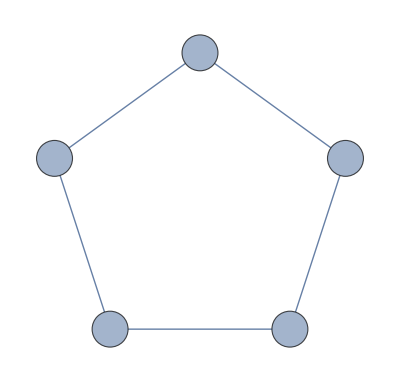

```mathematica
subdivideExample=CycleGraph[5,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

We will subdivide the edge {1,2}. To do this, we first need to introduce a vertex. We will give this vertex the name “1-2”. We apply ToString to the integers to create strings and combine them and the hyphen with the StringJoin (<>) operator. We use the VertexAdd function to add the vertex to the graph.

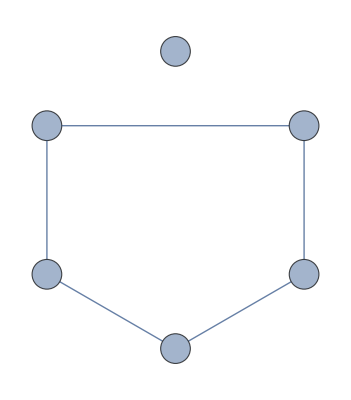

```mathematica
subdivideExampleB=VertexAdd[subdivideExample,ToString[1]<>"-"<>ToString[2]]
```

Note that Mathematica has moved the original vertices. We can put them back in place by assigning the VertexCoordinates option in the new graph to the positions of the original vertices obtained from GraphEmbedding. We just need to append a location for the new vertex, which will be at the end of the list of vertices. Note that we need to apply Graph to the result of the VertexAdd, since that function will not accept the options normally available to graphs.

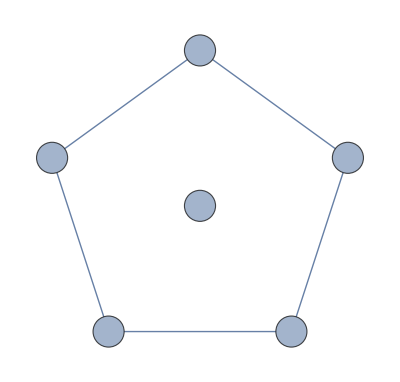

```mathematica
subdivideExampleB=Graph[VertexAdd[subdivideExample,ToString[1]<>"-"<>ToString[2]],VertexCoordinates->Append[GraphEmbedding[subdivideExample],{0,0}]]
```

Now, we move the new vertex along the edge which is to be deleted. This is done by using PropertyValue and averaging the positions of the existing vertices.

```mathematica
PropertyValue[{subdivideExampleB,"1-2"},VertexCoordinates]=(PropertyValue[{subdivideExample,1},VertexCoordinates]+PropertyValue[{subdivideExample,2},VertexCoordinates])/2
```

{-0.769421,-0.25}

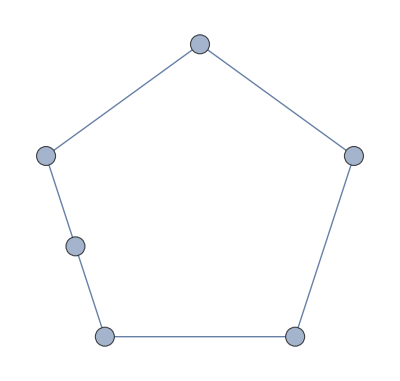

```mathematica
subdivideExampleB
```

Finally, we simply remove the original edge with EdgeDelete and add the new ones with EdgeAdd. Recall that the second argument of EdgeDelete must be given using the special symbols <-> (EscueEsc) or -> (EscdeEsc), not as a Rule (->).

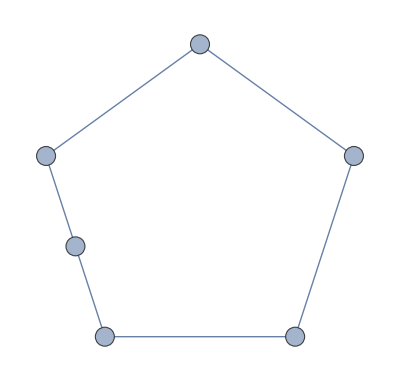

```mathematica
subdivideExampleB=EdgeDelete[subdivideExampleB,1->2];
subdivideExampleB=EdgeAdd[subdivideExampleB,{1->"1-2",2->"1-2"}]
```

Based on this example, we create the following function.

```mathematica
subdivideGraph::nonedge="Second argument must be an edge in the graph.";
subdivideGraph[G_Graph,E_Rule|E_UndirectedEdge]/;UndirectedGraphQ[G]:=Module[{H,e,newV,v},
If[Head[E]===Rule,
e=UndirectedEdge@@E,
e=E
];
If[!EdgeQ[G,e],Message[subdivideGraph::nonedge];Return[$Failed]];
newV=ToString[e[[1]]]<>"-"<>ToString[e[[2]]];
H=Graph[VertexAdd[G,newV],VertexCoordinates->Append[GraphEmbedding[G],{0,0}]];
PropertyValue[{H,newV},VertexCoordinates]=(PropertyValue[{H,e[[1]]},VertexCoordinates]+PropertyValue[{H,e[[2]]},VertexCoordinates])/2;
H=EdgeDelete[H,e];
H=EdgeAdd[H,{e[[1]]->newV,newV->e[[2]]}];
H
]
```

The inverse operation of elementary subdivision is referred to as smoothing. To be precise, let v be a vertex of degree 2 with neighbors u and w and such that u and w are not adjacent. We smooth the vertex v by deleting v and the edges incident to it and adding the edge {u,w}. Below, we have created a function to implement smoothing.

```mathematica
smoothGraph::vertx="Cannot smooth this vertex.";
smoothGraph[G_Graph,v_]/;UndirectedGraphQ[G]:=Module[{N,H,e},
N=AdjacencyList[G,v];
If[Length[N]≠2||EdgeQ[G,UndirectedEdge[N[[1]],N[[2]]]],Message[smoothGraph::vertx];Return[$Failed]];
H=VertexDelete[G,v];
e=UndirectedEdge[N[[1]],N[[2]]];
H=EdgeAdd[H,e];
H
]
```

As an example, we can smooth the vertex “1-2” added above.

```mathematica
smoothGraph[subdivideExampleB,"1-2"]
```

-Graphics-

The textbook defines graphs to be homeomorphic if they can be obtained from the same graph from a sequence of elementary subdivisions. It is clear that if G_1,G_2,G_3,…,G_n is a sequence of graphs, each of which can be obtained from the previous by an elementary subdivision, then G_n,…,G_3,G_2,G_1 is a sequence of graphs, each of which can be obtained from the previous by a smoothing. Hence, we can say that two graphs are homeomorphic if one can be transformed into the other by a sequence of elementary subdivisions and smoothings.

### Applying Kuratowski’s Theorem

Recall that Kuratowski’s theorem asserts that a graph is nonplanar if and only if it contains a subgraph homeomorphic to either K_(3,3) or K_5. Using the functions above and those for creating subgraphs, we can use Mathematica to manipulate a graph and confirm that it is nonplanar using Kuratowski’s theorem. We will illustrate this with the Petersen graph.

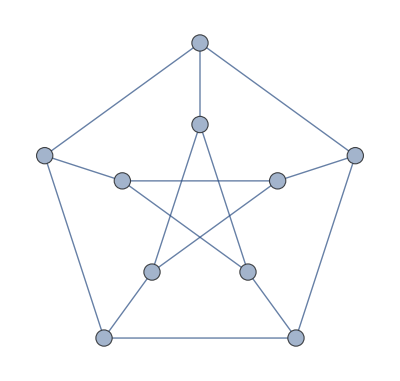

```mathematica
petersen=PetersenGraph[5,2,VertexSize->Medium,VertexLabels->Placed["Name",Center]]
```

First, we form the subgraph of the Petersen graph obtained by removing vertex 2 and the three edges incident to it.

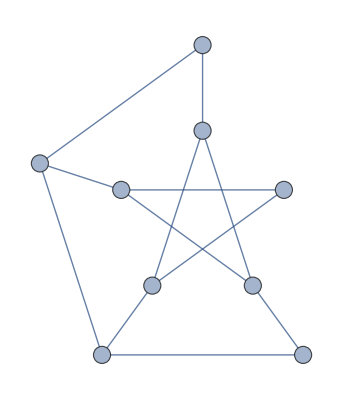

```mathematica
petersen1=VertexDelete[petersen,6]
```

Now, we notice that there are three vertices that are smoothable: 1, 7, and 10. That is to say, those three vertices have degree 2 and their neighbors are not adjacent.

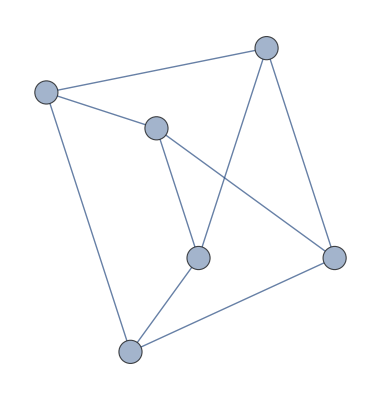

```mathematica
petersen2=smoothGraph[petersen1,1];petersen3=smoothGraph[petersen2,7];
petersen4=smoothGraph[petersen3,10]
```

We now observe that this graph has 6 vertices, each of which has degree 3, just like K_(3,3). Therefore, there is a definite possibility that this graph is K_(3,3). We confirm that is K_(3,3) with IsomorphicGraphQ.

```mathematica
IsomorphicGraphQ[petersen4,CompleteGraph[{3,3}]]
```

True

This demonstrates that the Petersen graph has a subgraph that is homeomorphic to K_(3,3) and hence is nonplanar.

## 10.8 Graph Coloring

In this section, we consider the problem of how to properly color a graph; that is, how to assign to each vertex of a graph a color such that no vertex has the same color as any of its neighbors.

It is worth noting that, in terms of computational complexity, Hamilton circuits and graph coloring are equivalently difficult problems.

We will create a function based on the algorithm described in the preface to Exercise 29 in Section 10.8 of the text. It can be shown that this algorithm will color a graph using at most one more color than the maximal degree of the graph. It is considered a greedy algorithm because it makes optimal choices at each step but never reconsiders its choices. That is to say, it does the best it can at every step but never backtracks to make improvements. Greedy algorithms often lead to good, but non-optimal, solutions.

The algorithm proceeds as follows. First, the vertices are sorted in order of descending degree. The first color is assigned to the first vertex in the list. Also assign color 1 to the first vertex in the list not adjacent to vertex 1, to the next vertex not adjacent to those already colored, etc. Then, move on to the second color. The first uncolored vertex in the list is assigned color 2, as are vertices further down the list not adjacent to ones previously assigned the second color. This continues until all of the vertices have been given a color.

Our first step in implementing this function will be to sort the list of vertices in decreasing order of degree. For this, we will make use of the Wolfram Language’s very flexible Sort function. With no additional instructions, this function will sort a list of numbers in increasing numerical order and a list of strings in lexicographical order. The Sort function can accept an optional argument that allows us to specify the way in which the list is sorted. Specifically, Sort takes as an argument a Boolean-valued function on two arguments and returns true if the first argument precedes the second.

For our graph coloring procedure, we will create a helper function that takes a Graph object and returns the sorted list of vertices.

```mathematica
sortVertices[G_Graph]:=Sort[VertexList[G],VertexDegree[G,#1]≥VertexDegree[G,#2]&]
```

In order for our algorithm to color the vertices of a graph, we need to decide on what colors to use. Here, we will use the first of the indexed color schemes.

```mathematica
ColorData[1]
```

ColorDataFunction[…]

The assertion that this ColorDataFunction has infinitely many colors is true in the sense that it will produce a color for any positive integer, although there is, of course, a limit on how many of them a person will be able to distinguish.

We now implement the greedy coloring algorithm.

```mathematica
greedyColorer[G_Graph]:=Module[{H=G,V,currentColor=0,colorFunction=ColorData[1],excludeSet,i},
V=sortVertices[H];
While[V≠{},currentColor++;
PropertyValue[{H,V[[1]]},VertexStyle]=colorFunction[currentColor];
excludeSet=VertexList[NeighborhoodGraph[H,V[[1]]]];
V=Delete[V,1];
i=1;
While[i≤Length[V],
If[!MemberQ[excludeSet,V[[i]]],
PropertyValue[{H,V[[i]]},VertexStyle]=colorFunction[currentColor];
excludeSet=Union[excludeSet,VertexList[NeighborhoodGraph[H,V[[i]]]]];
V=Delete[V,i],
i++
]
];
];
H
]
```

Note that the list V, which is initialized to the list of vertices, sorted in decreasing order of degree, is used to track which vertices still need to be assigned a color. When a vertex has been assigned a color, it is deleted from the list V using Delete. The Delete function removes from the list in the first argument the element at the position specified by the second argument.

The excludeSet variable is used to store all vertices which cannot be assigned the current color. Each time a vertex is assigned a color, it and all of its neighbors are added to the excludeSet. As the function looks down the list of vertices that still need to have a color assigned, it checks to see if they are in this set.

The index i, which controls the inner While loop, is incremented in the else clause of the If statement that tests to see if a vertex can be assigned the color. If the vertex at index i is assigned the color, then it is removed from the list V, and thus the index i refers to a different vertex (the vertex previously in position i+1).

As an example, we solve Exercise 29 of Section 10.8.

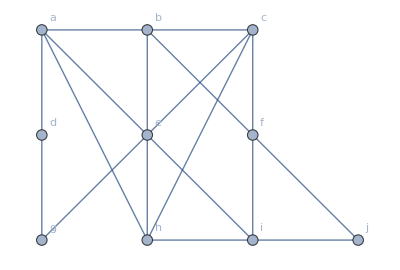

```mathematica
exercise29=Graph[{"a","b","c","d","e","f","g","h","i","j"},{"a"->"b","a"->"d","a"->"e","a"->"h","b"->"c","b"->"e","b"->"f","c"->"e","c"->"f","c"->"h","d"->"g","e"->"g","e"->"h","e"->"i","f"->"i","f"->"j","h"->"i","i"->"j"},DirectedEdges->False,VertexCoordinates->{{0,2},{1,2},{2,2},{0,1},{1,1},{2,1},{0,0},{1,0},{2,0},{3,0}},VertexLabels->"Name",VertexSize->Small]
```

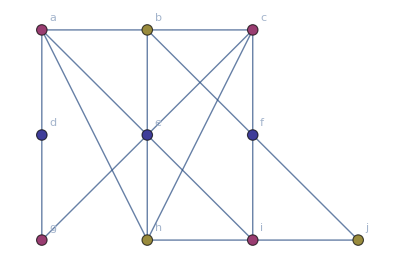

```mathematica
greedyColorer[exercise29]
```

## Solutions to Computer Projects and Computations and Explorations

### Computations and Explorations 1

Display all simple graphs with four vertices.

Solution: To solve this problem, we will generate all possible edge sets and then construct the graphs based on these edge sets. The possible edge sets are all of the subsets of the set of all possible edges, which we obtain from the complete graph on the vertices. We generalize the question and have our function create all the simple graphs on n vertices.

```mathematica
allGraphs[n_Integer]/;n>0:=Module[{cg,v,A={},V=Range[n],powerE,vCoords,E},
cg=CompleteGraph[n];
powerE=Subsets[EdgeList[cg]];
vCoords=GraphEmbedding[cg];
Do[AppendTo[A,Graph[V,E,VertexCoordinates->vCoords]],{E,powerE}];
A
]
```

Recall that the complete graph on n vertices has C(n,2) edges, so there are 2^(C(n,2)) graphs on n vertices. Thus, on 4 vertices, there are 64 graphs. For n = 3, there are only 8 graphs, which is more manageable.

We use the Partition function to break the list of all graphs into triples and then apply Grid with the Frame option in order to display the results in a useful way. The second argument to Partition is the size of the sublists (the rows) and the last specifies padding, which is needed to create sublists of equal size. The third argument is the offset, which equals the second in order to not repeat elements. The fourth argument allows for the last sublist to be padded.

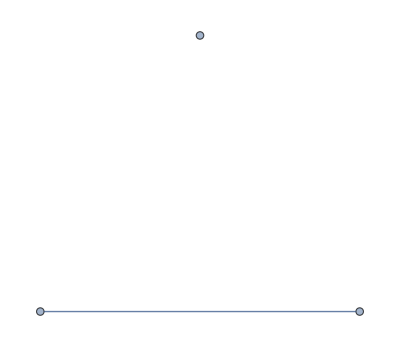
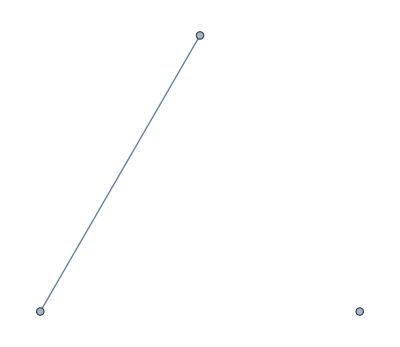
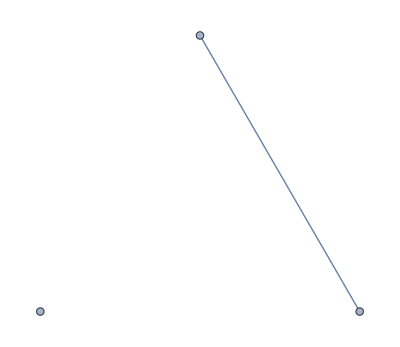
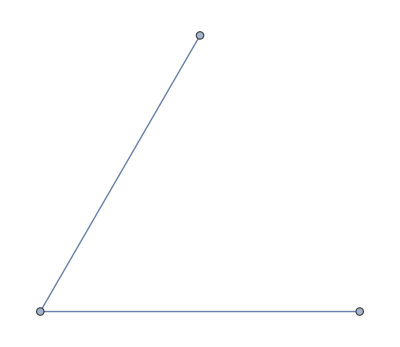
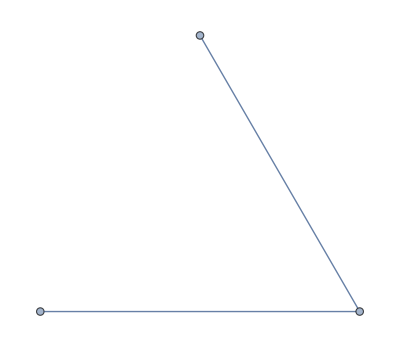
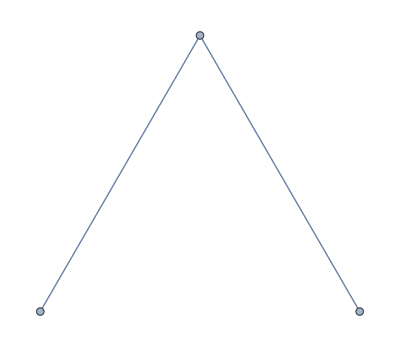

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[Partition[allGraphs[3],3,3,{1,1},Null],Frame->All]
```

### Computations and Explorations 2

Display a full set of nonisomorphic simple graphs with six vertices.

Solution: The solution to this exercise is very similar to the previous question. The only difference is that, once the list of graphs is generated, we remove those that are isomorphic to others by applying DeleteDuplicates with second argument IsomorphicGraphQ. This uses IsomorphicGraphQ to determine whether two elements are to be considered duplicates or not.

```mathematica
nonIsoGraphs[n_Integer]/;n>0:=Module[{cg,v,A={},V=Range[n],powerE,vCoords,E,i,G,j},
cg=CompleteGraph[n];
powerE=Subsets[EdgeList[cg]];
vCoords=GraphEmbedding[cg];
Do[AppendTo[A,Graph[V,E,VertexCoordinates->vCoords]]
,{E,powerE}];
DeleteDuplicates[A,IsomorphicGraphQ]
]
```

We apply this to five vertices, since six takes a bit more time to compute.

```mathematica
nonIso5=nonIsoGraphs[5];
```

```mathematica
Length[nonIso5]
```

34

We see that there are 34 nonisomorphic graphs on 5 vertices. Here are the first nine.

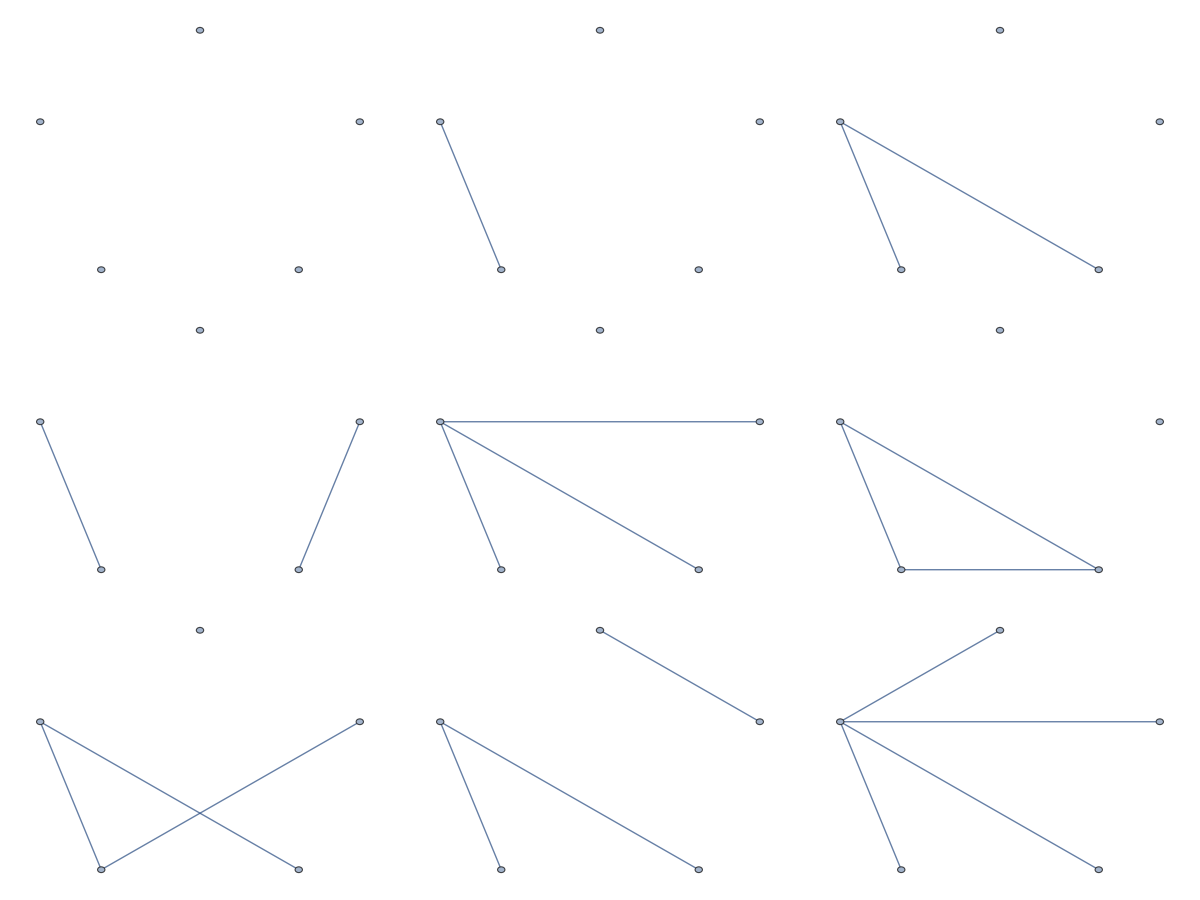

```mathematica
Grid[Partition[nonIso5[[1;;9]],3],Frame->All]
```

### Computations and Explorations 9

Generate at random simple graphs with 10 vertices. Stop when you have constructed one with an Euler circuit. Display an Euler circuit in this graph.

Solution: To generate the random graphs, we will use the RandomGraph function. By passing this function a list containing a number of vertices and a number of edges, it produces a graph with that number of vertices and edges. To display a random graph on 10 vertices and 15 edges, we enter the following:

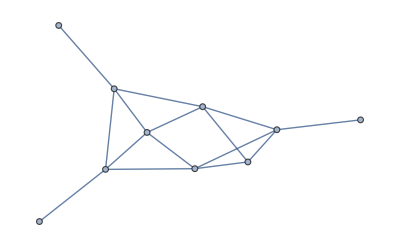

```mathematica
RandomGraph[{10,15}]
```

Alternatively, the argument to RandomGraph can be a graph distribution, which is a probability distribution on the sample space consisting of graphs. There are six built-in graph distributions. We will use the BernoulliGraphDistribution, which allows you to specify a number of vertices and a probability. The probability indicates the independent probability that an edge will appear between any two vertices. It requires two parameters, the number of vertices and the probability. The following constructs a random graph with 10 vertices and with each edge as likely to appear as not.

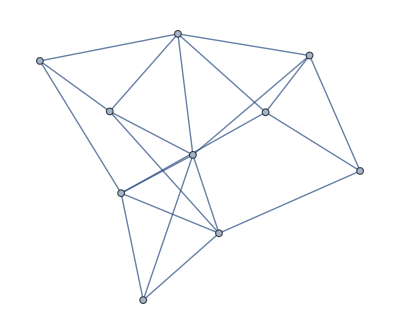

```mathematica
RandomGraph[BernoulliGraphDistribution[10,.5]]
```

RandomGraph also accepts an optional second argument, a positive integer, causing it to produce a list of that many random graphs.

Recall the description of the EulerianGraphQ function. When this function is given a graph, it returns true or false depending on the existence of an Euler circuit.

To satisfy the requirements of this problem, we use RandomGraph to generate a random graph G. Then, we test it for an Euler circuit using EulerianGraphQ. As long as the randomly generated graph does not have an Euler circuit, we continue generating new random graphs. We display the path using FindEulerianCycle and the animatePath function we created in Section 10.5.

```mathematica
generateEulerian[n_Integer]/;n>0:=Module[{G,path},
While[!EulerianGraphQ[G],G=RandomGraph[BernoulliGraphDistribution[n,.5]]];
animatePath[G,First[FindEulerianCycle[G]]]
]
```

```mathematica
generateEulerian[10]
```

### Computations and Explorations 13

Estimate the probability that a randomly generated simple graph with n vertices is connected for each possible integer n not exceeding ten by generating a set of random simple graphs and determining whether each is connected.

Solution: To solve this problem we will create a function that generates a number of random graphs of the specified size and counts the number that are connected. We use the RandomGraph function to create the random graphs and the ConnectedGraphQ function to test them for connectivity.

```mathematica
connectedProbability[n_Integer,max_Integer]/;n>0&&max>0:=Module[{G,i,count=0},
For[i=1,i≤max,i++,
G=RandomGraph[BernoulliGraphDistribution[n,.5]];
If[ConnectedGraphQ[G],count++]
];
count/max
]
```

```mathematica
Table[connectedProbability[i,100],{i,10}]
```

{1,9/20,53/100,13/25,18/25,81/100,87/100,24/25,97/100,97/100}

## Exercises

Write a function in the Wolfram Language to find all maximal matchings for a bipartite graph.

Write functions in the Wolfram Language for calculating the adjacency and incidence matrices for a pseudograph.

Write a function in the Wolfram Language for creating a pseudograph from an incidence matrix.

Write a function in the Wolfram Language to automate the creation of vertex-colored graphs to illustrate graph isomorphisms, as was done with the graphs from Example 11 at the end of Section 10.3 of this manual.

Write a function in the Wolfram Language to find all of the minimal edge cuts of a given graph.

Use Mathematica to construct all regular graphs of degree n, given a positive integer n. (Regular graph is defined in the Exercises for Section 10.2.)

For vertices u and v in a simple, undirected and connected graph G, the local vertex connectivity κ(u,v) is defined to be the minimum number of vertices that must be removed so that there is no path between vertex u and vertex v. Write a function in the Wolfram Language that calculates the local vertex connectivity of a graph and a pair of its vertices.

For vertices u and v in a simple, undirected and connected graph G, the local edge connectivity λ(u,v) is defined to be the minimum number of edges that must be removed so that there is no path between vertex u and vertex v. Write a function in the Wolfram Language that calculates the local edge connectivity of a graph and a pair of its vertices.

Write a function in the Wolfram Language that computes the thickness of a nonplanar simple graph (see the Exercises in Section 10.7 for a definition of thickness).

Write a function in the Wolfram Language for finding an orientation of a simple graph. (An orientation of a graph is defined in the Supplementary Exercises of Chapter 10.)

Write a function in the Wolfram Language for finding the bandwidth of a simple graph. (The bandwidth of a graph is defined in the Supplementary Exercises of Chapter 10.)

Write a function in the Wolfram Language for finding the radius and diameter of a simple graph. (The radius and diameter of a graph are defined in the Supplementary Exercises of Chapter 10.)

Use Mathematica to find the minimum number of queens controlling an n×n chessboard for as many values of n as you can. Make use of the concept of a dominating set, described in the Supplementary Exercises of Chapter 10.

Write a function in the Wolfram Language for finding all self-complementary graphs on n vertices. (A self-complementary graph is a graph which is isomorphic to its own complement.) Use your function to display the self-complementary graphs for as large a n as possible.

Write a function in the Wolfram Language that finds a total coloring for a graph. A total coloring of a graph is an assignment of a color to each vertex and each edge such that: (a) no pair of adjacent vertices have the same color; (b) no two edges with a common endpoint have the same color; and (c) no edge has the same color as either of its endpoints.

A sequence of positive integers is called graphic if there is a simple graph that has this sequence as its degree sequence. In this context, the degree sequence of a graph is the nondecreasing sequence made up of the degrees of the vertices of the graph. Develop a function in the Wolfram Language for determining whether a sequence of positive integers is graphic and, if it is, to construct a graph with this degree sequence.